# PhenomTHM-RDFits

```mathematica
Quit[]
```

## Setup

### Setup paths and other notebook folders

```mathematica
MetaDir2="~/SVN/PhenomHM/bin/";
notdir=NotebookDirectory[];
l2dir=NotebookDirectory[]<>"/l2";
```

```mathematica
markers={"●","■","◆","▲","▼","○","□","◇","△","▽"};
```

```mathematica
colors=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
colors={RGBColor[0.,0.62,0.53],RGBColor[1.,0.,0.38],RGBColor[0.,0.73,1.],RGBColor[1.,0.71,0.],RGBColor[0.46,0.,0.62],RGBColor[0.68,0.69,0.],RGBColor[0.62,0.,0.13],RGBColor[1.,0.53,0.25],RGBColor[0.,0.62,0.53],RGBColor[1.,0.,0.38],RGBColor[0.,0.73,1.],RGBColor[1.,0.71,0.],RGBColor[0.46,0.,0.62],RGBColor[0.68,0.69,0.],RGBColor[0.62,0.,0.13],RGBColor[1.,0.53,0.25]}
```

{RGBColor[0., 0.62, 0.53],RGBColor[1., 0., 0.38],RGBColor[0., 0.73, 1.],RGBColor[1., 0.71, 0.],RGBColor[0.46, 0., 0.62],RGBColor[0.68, 0.69, 0.],RGBColor[0.62, 0., 0.13],RGBColor[1., 0.53, 0.25],RGBColor[0., 0.62, 0.53],RGBColor[1., 0., 0.38],RGBColor[0., 0.73, 1.],RGBColor[1., 0.71, 0.],RGBColor[0.46, 0., 0.62],RGBColor[0.68, 0.69, 0.],RGBColor[0.62, 0., 0.13],RGBColor[1., 0.53, 0.25]}

### Load packages

```mathematica
<<NRFits.m
<<SXSFormat.m
<<BBHReduce.m
<<ParfileGen.m
<<DataFits.m
<<NRWaves.m
<<NRMatch.m
<<NRUnits.m
<<MCMC.m
```

Get::noopen: Cannot open NinjaBase`.

Needs::nocont: Context NinjaBase` was not created when Needs was evaluated.

Import::nffil: File ~/SVN/WaveGearData/Detectors/H1L1-AVERAGE_PSD-1127271617-1027800.txt.gz not found during Import.

Interpolation::inhr: Requested order is too high; order has been reduced to {0}.

```mathematica
(*Global`PhenomDir = "~/SVN/Phenom/";
<< "~/SVN/Phenom/IMRPhenomD/IMRPhenomD.m"
*)
```

```mathematica
(*should be the lal version*)
(*Get[FileNameJoin[{"/Users/xisco/SVN/Phenom/Sebastian/","Fits_To_Hybrid","IMRPhenomDHybridsv2Hybrids0010.m"}]];*)
```

```mathematica
plotColors=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

### Imports

From: http://www.phy.olemiss.edu/~berti/ringdown/. 
l,m,n ,f1, f2,f3,q1,q2,q3: m w= f1 + f2 (1-a/M)^f3
and 
https : // centra.tecnico.ulisboa.pt/network/grit/files/ringdown/

```mathematica
notdir<>"/fitcoeffsWEB.dat"
```

/Users/xisco/Work/INFN/Work/Rdown//fitcoeffsWEB.dat

```mathematica
lmnf1f2f3q1q2q3=Select[Import[notdir<>"/fitcoeffsWEB.dat"],UnsameQ[#,{}]&];
l2mnfile=notdir;
```

## Functions

### General functions

```mathematica
Clear[ImportH5Datasets];
(*code by Rafel, should migrate to NRCore after testing *)
ImportH5Datasets[file_String,dataset_String]:=Module[{nameS,l,out},
nameS=StringPartition[dataset,1];
l=Length@nameS;
If[MemberQ[Import[file,{"HDF5","Datasets"}], dataset],
   Import[file,{"HDF5","Datasets",dataset}],
   Import[file,{"HDF5","Datasets",StringJoin@Table[If[ToCharacterCode[nameS[[i]],"Unicode"][[1]]>912,"\\:0"<>ToUpperCase[StringSplit@IntegerString[ToCharacterCode[nameS[[i]],"Unicode"][[1]],16]][[1]],nameS[[i]]],{i,l}]}]
]
]
```

```mathematica
PlanckTaper[t_?VectorQ,t1_,t2_]:=Module[{tmid=Select[t,t1<#<t2&]},Join[
ConstantArray[0,Length@Select[t,#≤t1&]],
1/(Exp[(t2-t1)/(tmid-t1)+(t2-t1)/(tmid-t2)]+1),
ConstantArray[1,Length@Select[t,#≥t2&]]
]];
PlanckTaper[t_?NumberQ,t1_,t2_]:=
Piecewise[{{0,t≤t1},
{1/(Exp[(t2-t1)/(t-t1)+(t2-t1)/(t-t2)]+1),t1<t<t2},
{1,t≥ t2}
}];
```

```mathematica
OrientMax[wave_,OptionsPattern[{Threshold->10^(-4)}]]:=Module[{times,modWave,maxPos,timeMax,i,maxVal,mitimes,matimes},
maxVal=Max[Abs[wave[[;;,2]]]];
times=Select[wave,Abs[#[[2]]]>maxVal*OptionValue[Threshold]&][[;;,1]];
mitimes=Min[times];
matimes=Max[times];
modWave=Sort[Select[wave,mitimes≤#[[1]]≤matimes&]];
maxPos=Position[Abs[modWave[[;;,2]]],maxVal][[1,1]];
timeMax=modWave[[maxPos,1]];
Transpose[{modWave[[;;,1]]-timeMax,modWave[[;;,2]]}]
];
```

```mathematica
With[{newopts={fCut,fLowFrac,DataPostProc,Variabledf,NumDf,dt}},
Unprotect[newopts];
ClearAll/@newopts;
(#=#)&/@newopts;
Protect[newopts]];

Options[InvFFT]={fCut->0.15,fLowFrac->0.8,DataPostProc->True,Threshold->10^(-4),Verbose->False,Variabledf->True,NumDf->False};


InvFFT[PhenomPhase_,PhenomAmp_,flow_,dt_,OptionsPattern[]]:=
Module[{Dphase,f,fstart=flow*OptionValue[fLowFrac],phasediffShift,dfMax,wf,df,nPts,totT,exp2,fmax,phenomTab,mult,toInv,timeWf,t1,Dfstart,Dfcut,aux},

If[OptionValue[NumDf],
aux=Transpose[{#,PhenomPhase[#]}]&/@((Range[0.9,1.1,0.01]*#&/@{fstart,OptionValue[fCut]}));
aux=Interpolation/@aux;
Dphase=D[#[f],f]&/@aux;
{Dfstart,Dfcut}={Dphase[[1]]/.f->fstart,Dphase[[2]]/.f->OptionValue[fCut]};
,
Dphase[f_]=D[PhenomPhase[f], f];
Dfstart=Dphase[fstart];
Dfcut=Dphase[OptionValue[fCut]]
];
phasediffShift=(Dfstart+Dfcut)/2;
dfMax=π/(Dfstart-phasediffShift);
df=Abs[dfMax/2];

wf[f_]:=PhenomAmp[f] Exp[I (PhenomPhase[f]-phasediffShift f)];

If[OptionValue[Variabledf],
exp2=Log[Ceiling[1/(df dt)]]/Log[2];
exp2=If[Mod[exp2,1]<0.4,Floor[exp2],Ceiling[exp2]];
nPts=2^exp2,
nPts=Ceiling[1/(df dt)]
];
totT=nPts dt;
df=1/totT;
fmax = 1/(2 dt);

If[OptionValue[Verbose],
Print["number of points = ",nPts];
Print["df = ",df];
Print["predicted maximum for df = ",Abs[dfMax]]
];

phenomTab=PadLeft[PadRight[wf[Range[df,fmax,df]],nPts-1],nPts];
mult=PadRight[N[PlanckTaper[Range[0,fmax,df],fstart,flow]],nPts,1];
toInv=phenomTab*mult;
timeWf=df InverseFourier[toInv,FourierParameters->{-1,1}];

timeWf=Transpose[{Join[t1=Range[0,totT/2,dt],Range[Last[t1]+dt,totT-dt,dt]-totT],timeWf}];

If[OptionValue[DataPostProc],
OrientMax[timeWf,Threshold->OptionValue[Threshold]],
timeWf
]
];
```

```mathematica
Options[PlotTimeDomain]=Join[Options[InvFFT],{dt->2.5,PlotRange->All,FrameLabel->{"t/M","h_+"},ImageSize->800,AspectRatio->1/6,FrameStyle->Thick,FrameTicksStyle->Thick,Frame->True},FilterRules[Options[ListLinePlot],Except[{FrameLabel,ImageSize,PlotRange,AspectRatio,FrameStyle,FrameTicksStyle}]]];

PlotTimeDomain[phase_,amp_,flow_,fRange_,opts:OptionsPattern[Options[PlotTimeDomain]]]:=Module[{data},
data=InvFFT[phase,amp,flow,OptionValue[dt],FilterRules[{opts},Options[InvFFT]]];
ListLinePlot[{{#[[1]],Re[#[[2]]]}&/@Select[data,fRange[[1]]≤#[[1]]≤fRange[[2]]&](*,{#[[1]],Abs[#[[2]]]}&/@Select[data,fRange[[1]]≤#[[1]]≤fRange[[2]]&]*)},FilterRules[Join[{opts},Options[Options[PlotTimeDomain]]],Options[ListLinePlot]]]
];
```

### Rdown Lionel

```mathematica
Module[{TakeColumn,
RootDirQNM,tmpPlus,tmpMinus,tmpData},
	tmpData=Import[FileNameJoin[{MetaDir2,"FNM_L2M2_ExtendedData.dat"}],"Table"];
	iFring22=Interpolation[tmpData[[;;,{1,2}]]];
	iFdamp22=Interpolation[tmpData[[;;,{1,3}]]];
]
```

```mathematica
Module[{TakeColumn,
RootDirQNM,tmpPlus,tmpMinus,tmpData},
	tmpData=Import[FileNameJoin[{MetaDir2,"FNM_L2M1_ExtendedData.dat"}],"Table"];
	iFring21=Interpolation[tmpData[[;;,{1,2}]]];
	iFdamp21=Interpolation[tmpData[[;;,{1,3}]]];
]
```

```mathematica
Module[{TakeColumn,
RootDirQNM,tmpPlus,tmpMinus,tmpData},
	tmpData=Import[FileNameJoin[{MetaDir2,"FNM_L3M3_ExtendedData.dat"}],"Table"];
	iFring33=Interpolation[tmpData[[;;,{1,2}]]];
	iFdamp33=Interpolation[tmpData[[;;,{1,3}]]];
]
```

```mathematica
Module[{TakeColumn,
RootDirQNM,tmpPlus,tmpMinus,tmpData},
	tmpData=Import[FileNameJoin[{MetaDir2,"FNM_L3M2_ExtendedData.dat"}],"Table"];
	iFring32=Interpolation[tmpData[[;;,{1,2}]]];
	iFdamp32=Interpolation[tmpData[[;;,{1,3}]]];
]
```

```mathematica
Module[{TakeColumn,
RootDirQNM,tmpPlus,tmpMinus,tmpData},
	tmpData=Import[FileNameJoin[{MetaDir2,"FNM_L4M4_ExtendedData.dat"}],"Table"];
	iFring44=Interpolation[tmpData[[;;,{1,2}]]];
	iFdamp44=Interpolation[tmpData[[;;,{1,3}]]];
]
```

```mathematica
Module[{TakeColumn,
RootDirQNM,tmpPlus,tmpMinus,tmpData},
	tmpData=Import[FileNameJoin[{MetaDir2,"FNM_L4M3_ExtendedData.dat"}],"Table"];
	iFring43=Interpolation[tmpData[[;;,{1,2}]]];
	iFdamp43=Interpolation[tmpData[[;;,{1,3}]]];
]
```

```mathematica
Module[{TakeColumn,
RootDirQNM,tmpPlus,tmpMinus,tmpData},
	tmpData=Import[FileNameJoin[{MetaDir2,"FNM_L4M2_ExtendedData.dat"}],"Table"];
	iFring42=Interpolation[tmpData[[;;,{1,2}]]];
	iFdamp42=Interpolation[tmpData[[;;,{1,3}]]];
]
```

```mathematica
Module[{TakeColumn,
RootDirQNM,tmpPlus,tmpMinus,tmpData},
	tmpData=Import[FileNameJoin[{MetaDir2,"FNM_L4M1_ExtendedData.dat"}],"Table"];
	iFring41=Interpolation[tmpData[[;;,{1,2}]]];
	iFdamp41=Interpolation[tmpData[[;;,{1,3}]]];
]
```

```mathematica
fring22[η_,χ1_,χ2_]:=iFring22[FinalSpinUIB2017[η,χ1,χ2]]/(2π (1.-EradUIB2017[η,χ1,χ2]));
fdamp22[η_,χ1_,χ2_]:=iFdamp22[FinalSpinUIB2017[η,χ1,χ2]]/(2π (1.-EradUIB2017[η,χ1,χ2]));
```

```mathematica
fring21[η_,χ1_,χ2_]:=iFring21[FinalSpinUIB2017[η,χ1,χ2]]/(2π (1.-EradUIB2017[η,χ1,χ2]));
fdamp21[η_,χ1_,χ2_]:=iFdamp21[FinalSpinUIB2017[η,χ1,χ2]]/(2π (1.-EradUIB2017[η,χ1,χ2]));
```

```mathematica
fring33[η_,χ1_,χ2_]:=iFring33[FinalSpinUIB2017[η,χ1,χ2]]/(2π (1.-EradUIB2017[η,χ1,χ2]));
fdamp33[η_,χ1_,χ2_]:=iFdamp33[FinalSpinUIB2017[η,χ1,χ2]]/(2π (1.-EradUIB2017[η,χ1,χ2]));
```

```mathematica
fring32[η_,χ1_,χ2_]:=iFring32[FinalSpinUIB2017[η,χ1,χ2]]/(2π (1.-EradUIB2017[η,χ1,χ2]));
fdamp32[η_,χ1_,χ2_]:=iFdamp32[FinalSpinUIB2017[η,χ1,χ2]]/(2π (1.-EradUIB2017[η,χ1,χ2]));
```

```mathematica
fring44[η_,χ1_,χ2_]:=iFring44[FinalSpinUIB2017[η,χ1,χ2]]/(2π (1.-EradUIB2017[η,χ1,χ2]));
fdamp44[η_,χ1_,χ2_]:=iFdamp44[FinalSpinUIB2017[η,χ1,χ2]]/(2π (1.-EradUIB2017[η,χ1,χ2]));
```

```mathematica
fring43[η_,χ1_,χ2_]:=iFring43[FinalSpinUIB2017[η,χ1,χ2]]/(2π (1.-EradUIB2017[η,χ1,χ2]));
fdamp43[η_,χ1_,χ2_]:=iFdamp43[FinalSpinUIB2017[η,χ1,χ2]]/(2π (1.-EradUIB2017[η,χ1,χ2]));
```

```mathematica
fring42[η_,χ1_,χ2_]:=iFring42[FinalSpinUIB2017[η,χ1,χ2]]/(2π (1.-EradUIB2017[η,χ1,χ2]));
fdamp42[η_,χ1_,χ2_]:=iFdamp42[FinalSpinUIB2017[η,χ1,χ2]]/(2π (1.-EradUIB2017[η,χ1,χ2]));
```

```mathematica
fring41[η_,χ1_,χ2_]:=iFring41[FinalSpinUIB2017[η,χ1,χ2]]/(2π (1.-EradUIB2017[η,χ1,χ2]));
fdamp41[η_,χ1_,χ2_]:=iFdamp41[FinalSpinUIB2017[η,χ1,χ2]]/(2π (1.-EradUIB2017[η,χ1,χ2]));
```

```mathematica
amp220[η_]:=ωrdown[2,2,0,η,0,0][[1]]^2(0.9252 η +0.1323 η^2)
```

```mathematica
amp221[η_]:=ωrdown[2,2,1,η,0,0][[1]]^2(0.1275 η Exp[5.3106 I]+1.1882 Exp[0.4873 I] η^2+8.2709 Exp[3.3895 I]η^3 +26.2329 Exp[0.1372 I ]η^4)
```

### Berti & Vitor’s data (fits for n>=3 do not work so well)

```mathematica
ωrdown[l_,m_,n_,η_,χ1_,χ2_]:=Module[{f1,f2,f3,q1,q2,q3,wr,q,τ},

{f1,f2,f3}=Select[lmnf1f2f3q1q2q3,#[[1]]==l&&#[[2]]==m&&#[[3]]==n&][[1,4;;6]];
{q1,q2,q3}=Select[lmnf1f2f3q1q2q3,#[[1]]==l&&#[[2]]==m&&#[[3]]==n&][[1,7;;9]];

(* Notice the factor 1/M ! *)
wr=1/(1-EradUIB2017[η,χ1,χ2])(f1+f2(1-FinalSpinUIB2017[η,χ1,χ2])^f3);
(*wr=(f1+f2(1-FinalSpinUIB2017[η,χ1,χ2])^f3);*)
(*q=1/(1-EradUIB2017[η,χ1,χ2])(q1+q2(1-FinalSpinUIB2017[η,χ1,χ2])^q3);*)
q=(q1+q2(1-FinalSpinUIB2017[η,χ1,χ2])^q3);

(* Notice the factor M ! *)
τ=1/(wr/(2 q))*1/(1-EradUIB2017[η,χ1,χ2]);
{wr,τ(1-EradUIB2017[η,χ1,χ2])}
]
```

```mathematica
ωlmn[l_,m_,n_,η_,χ1_,χ2_]:=Module[{file,data,sp,fmass,fχ,χωτ,ω,τ,llim,ulim},

If[n≤7,
file=l2mnfile<>"l"<>ToString[l]<>"/n"<>ToString[n+1]<>"l"<>ToString[l]<>"m"<>ToString[m]<>".dat";,
file=l2mnfile<>"l"<>ToString[l]<>"/n7l"<>ToString[l]<>"m"<>ToString[m]<>".dat"];
data=Import[file];
χωτ=TakeColumn[data,{1,2,3}];

fmass=1-EradUIB2017[η,χ1,χ2];
fχ=Abs@FinalSpinUIB2017[η,χ1,χ2];

ulim=Flatten[Select[χωτ,#[[1]]≥fχ&,1]];
llim=Flatten[Select[χωτ,#[[1]]-ulim[[1]]<0&][[-1]]];
ω=Mean[Join[{ulim},{llim}]][[2]]/fmass;
τ=Mean[(Abs[1/Join[{ulim},{llim}]]*fmass)][[-1]];
{ω,τ}
]
```

```mathematica
EradUIB2017[η_,χ1_,χ2_]:=Module[{m1,m2,S},
m1=1/2 (1+Sqrt[1-4 η]);
m2=1/2 (1-Sqrt[1-4 η]);

S= (m1^2 χ1 + m2^2 χ2)/(m1^2 + m2^2);

(((1-(2 Sqrt[2])/3) η+0.5609904135313374 η^2-0.84667563764404 η^3+3.145145224278187 η^4) (1+S^3 (-0.6320191645391563+ 4.952698546796005 η-10.023747993978121 η^2)+S^2 (-0.17762802148331427+ 2.176667900182948 η^2)+S (-0.13084389181783257- 1.1387311580238488 η+5.49074464410971 η^2)))/(1+S (-0.9919475346968611+ 0.367620218664352 η+4.274567337924067 η^2))
-0.01978238971523653 S (1-4.91667749015812 η) (1-4 η)^0.5 η (χ1-χ2)-0.09803730445895877 (1-4 η)^0.5 (1-3.2283713377939134 η) η^2 (χ1-χ2)+0.01118530335431078 η^3 (χ1-χ2)^2]
```

```mathematica
ωrdownV[l_,m_,n_,η_,χ1_,χ2_]:=Module[{f1,f2,f3,q1,q2,q3,wr,q,τ,fitw,fitτ},

If[n==0,fitw=1.3124462680551807-0.9465368447830794 (1-FinalSpinUIB2017[η,χ1,χ2])^0.16544069349411075;fitτ=8.72679258648556+2.062638485798269(1-FinalSpinUIB2017[η,χ1,χ2])^-0.5368622990606623];
If[n==1,fitw=1.2628387466870021-0.9232507086685433 (1-FinalSpinUIB2017[η,χ1,χ2])^0.1863877143281106;fitτ=2.8213560605369516+0.7105825957759406(1-FinalSpinUIB2017[η,χ1,χ2])^-0.5329551895458052];
If[n==2,fitw=1.218420795416322-0.923808481205012 (1-FinalSpinUIB2017[η,χ1,χ2])^0.21351296514617202;fitτ=1.470962507175263+0.550840982855238(1-FinalSpinUIB2017[η,χ1,χ2])^-0.48959769486350063];
If[n==3,fitw=1.219474986820303-0.9746812707817573 (1-FinalSpinUIB2017[η,χ1,χ2])^0.22552357676089377;fitτ=1.0001780702219651+0.3979067412394586(1-FinalSpinUIB2017[η,χ1,χ2])^-0.49119657589588367];
If[n==4,fitw=1.2689227939334176-1.06808616261201 (1-FinalSpinUIB2017[η,χ1,χ2])^0.21631168043420593;fitτ=0.7295447646489809+0.3271623619484011(1-FinalSpinUIB2017[η,χ1,χ2])^-0.4828133641299889];
If[n==5,fitw=0.5656444197237062-0.42237454078357145 (1-FinalSpinUIB2017[η,χ1,χ2])^0.8776885646754617;fitτ=1.595702650677585-0.7939644446955427 (1-FinalSpinUIB2017[η,χ1,χ2])^0.40718756621523167];
If[n==6,fitw=1.129495727889861-1.0043930197672468 (1-FinalSpinUIB2017[η,χ1,χ2])^0.29091409018088216;fitτ=0.281570903519987+0.3889708435426097 (1-FinalSpinUIB2017[η,χ1,χ2])^-0.4286902063547559];
If[n==7,fitw=1.0378370100854661-0.9455050036984939 (1-FinalSpinUIB2017[η,χ1,χ2])^0.36070951538498824;fitτ=0.250708716225119+0.323685466665891(1-FinalSpinUIB2017[η,χ1,χ2])^-0.4283465855669324];
wr=fitw/(1-EradUIB2017[η,χ1,χ2]);
τ=fitτ*(1-EradUIB2017[η,χ1,χ2]);
{wr,τ}
]
```

### Spherical harmonics Yslm

```mathematica
Eth[n_,f_] := - Sin[t]^n (D[f/Sin[t]^n,t]+I D[f/Sin[t]^n,p]/Sin[t])
Yp1[l_,m_]:= FullSimplify[Sqrt[ (l-1)!/(l+1)!]Eth[0,SphericalHarmonicY[l,m,t,p]]]
Yp2[l_,m_]:= FullSimplify[Sqrt[ (l-2)!/(l+2)!]Eth[1,Eth[0,SphericalHarmonicY[l,m,t,p]]]]

Ethbar[n_,f_] := - Sin[t]^(-n) (D[f Sin[t]^n,t]-I D[f Sin[t]^n,p]/Sin[t])
Ym1[l_,m_]:= FullSimplify[Sqrt[ (l-1)!/(l+1)!](-1)^(-1) Ethbar[0,SphericalHarmonicY[l,m,t,p]]]
Ym2[l_,m_]:= FullSimplify[Sqrt[ (l-2)!/(l+2)!](-1)^(-2)Ethbar[-1,Ethbar[0,SphericalHarmonicY[l,m,t,p]]]]
```

```mathematica
(* same source, direct formula using Wigner d-functions *)
wd[n_,l_,m_]:=Sum[
(-1)^i  Sqrt[(l+m)! (l-m)! (l+n)! (l-n)!] / ((l+m-i)!(l-n-i)!i!(i+n-m)!)
Cos[t/2]^(2l+m-n-2i)Sin[t/2]^(2i+n-m),
{i,Max[0,m-n],Min[l+m,l-n]}
]
Ydirect[n_,l_,m_]:=FullSimplify[(-1)^n  Sqrt[(2l+1)/(4Pi)] wd[-n,l,m]E^(I m p)]
```

### RD Fit Functions (SEOBNRv4 paper + my fit)

```mathematica
RDownAmpSEOBNRv4[NRwave_,params_,mode_,OptionsPattern[{"Verbose"->False,"Tmax"->""}]]:=Module[{η,χ1,χ2,χ,c1f,c2f,c1c,c2c,tmatch,vtmatch,t,eq1,eq2,sol,
h22Amp,Amp22,h22AmpDer,NRh22Amp,NRh22AmpInt,NRh22AmpIntDer,fdamp,y,l,m,fdamplm,verbose,tmax},

(* Options *)
verbose=OptionValue["Verbose"];
tmax=OptionValue["Tmax"];

(* Physical parameters: sym. massratio and dimensionless spins such m1>m2*)
{η,χ1,χ2}=params;
{l,m}=mode;

(* Ansatz employed in PHYSICAL REVIEW D 95, 044028 (2017) (SEOBNRv4)*)
Amp22[t_]:=c1c Tanh[c1f(t-tmatch)+c2f]+c2c ;
h22Amp[t_]:=η Amp22[t]Exp[-(t-tmatch)/fdamp];
h22AmpDer[t_]:=Evaluate[D[h22Amp[t],t]];

(* NR amplitude *)
NRh22Amp=Abs0DStructs@NRwave;
NRh22AmpInt=Interpolation@NRh22Amp;
NRh22AmpIntDer=D[NRh22AmpInt@t,t]/.y_[t_]->y;

(* Damping time using Lionel London fits to NR. The 2π transforms it to ω *)
fdamplm=ToExpression["fdamp"<>ToString@l<>ToString@m];
(*fdamp=Abs[1/(2π fdamplm[η,χ1,χ2])];*)
fdamp=ωrdown[2,2,0,η,χ1,χ2][[2]];
χ=0.5(χ1+χ2)+0.5(χ1-χ2)/(1-2η)Sqrt[1-4 η];

(* Phenomenological fits as in PHYSICAL REVIEW D 95, 044028 (2017) *)
c1f=−0.0893454 η^2+0.0612892η+0.00146142 η χ -0.0136459 χ^2 -0.0196758χ+0.0830664;
c2f=-1.82173 η^2 -5.25339 η^2 χ+2.40203η χ+1.39777η -0.371365χ -0.623953;

(* Matching time consistent with peak luminosity *)
If[Not@NumberQ@tmax,tmatch=TimeOfMaximum[NRwave],tmatch=TimeOfMaximum[NRwave]+tmax];
If[verbose,Print["Match time: ",tmatch]];
vtmatch=ValueOfMaximum[NRwave];

(* Applying C^1 continuity *)
eq1={h22Amp[tmatch]==vtmatch};
eq2={h22AmpDer[tmatch]==NRh22AmpIntDer[tmatch]};

sol={c1c,c2c}/.NSolve[Join[eq1,eq2],{c1c,c2c}];
{c1c,c2c}=Flatten@sol;

(* Plot the amplitude when verbose=True *)
If[verbose, Print@{Plot[{h22Amp[t],NRh22AmpInt@t},{t,tmatch,tmatch+50},Frame->True,FrameLabel->{"t","|h"<>ToString@l<>ToString@m<>"(t)|"},
FrameStyle->Directive[Bold,Black,14],PlotLegends->{"Fit","Data"},ImageSize->450],Plot[{h22Amp[t]/NRh22AmpInt@t},{t,tmatch,tmatch+50},Frame->True,FrameLabel->{"t","Δϕ"<>ToString@l<>ToString@m<>"(t)"},
FrameStyle->Directive[Bold,Black,14],PlotLegends->{"Fit/Data"},ImageSize->450]}];

{c1f,c2f,c1c,c2c,fdamp,tmatch}
];
```

```mathematica
RDownPhaseSEOBNRv4[NRwave_,params_,mode_,OptionsPattern[{"Verbose"->False,"Tmax"->""}]]:=Module[{η,χ1,χ2,χ,d1f,d2f,d1c,d2c,ϕ0,tmatch,vtmatch,t,eq1,eq2,sol,
h22Phase,h22PhaseDer,NRh22Phase,NRh22PhaseInt,NRh22PhaseIntDer,fRD,y,l,m,fRDlm,verbose,xx,yy,tmax},

(* Options *)
verbose=OptionValue["Verbose"];
tmax=OptionValue["Tmax"];

(* Physical parameters: sym. massratio and dimensionless spins such m1>m2*)
{η,χ1,χ2}=params;
{l,m}=mode;

(* Ansatz employed in PHYSICAL REVIEW D 95, 044028 (2017) (SEOBNRv4). The l/2 factor does not seem to work but does not affect the 22 mode *)
h22Phase[t_]:=(ϕ0 -l/2. d1c Log[(1+d2f Exp[-d1f(t-tmatch)])/(1+d2f)]+fRD(t-tmatch));
(*h22Phase[t_]:=(ϕ0 -l/2. d1c Log[(1+d2f Exp[-d1f(t-tmatch)])/(1+d2f)]);*)
h22PhaseDer[t_]:=Evaluate[D[h22Phase[t],t]];

(* NR amplitude *)
NRh22Phase=Arg0DStructs@NRwave;
If[NRh22Phase[[Round[Length@NRh22Phase/2],2]]<0,NRh22Phase=NRh22Phase/.{xx_,yy_}->{xx,-yy}];
NRh22PhaseInt=Interpolation@NRh22Phase;
NRh22PhaseIntDer=D[NRh22PhaseInt@t,t]/.y_[t_]->y;

(* Damping time using Lionel London fits to NR. The 2π transforms it to ω *)
fRDlm=ToExpression["fring"<>ToString@l<>ToString@m];
(*fRD=Abs[2π fRDlm[η,χ1,χ2]];*)
fRD=ωrdown[2,2,0,η,χ1,χ2][[1]];
χ=0.5(χ1+χ2)+0.5(χ1-χ2)/(1-2η)Sqrt[1-4 η];

(* Phenomenological fits as in PHYSICAL REVIEW D 95, 044028 (2017) *)
d1f=−0.808987 η^2+ 0.263456η-  0.120853η χ - 0.0244358χ^2 +0.00779176χ+0.147584;
d2f=+17.5646 η^2 -6.99396 η -9.61861 η χ+ 0.581626χ^2 +3.13067χ +2.46654;

(* Matching time consistent with peak luminosity *)
If[Not@NumberQ@tmax,tmatch=TimeOfMaximum[NRwave],tmatch=TimeOfMaximum[NRwave]+tmax];
ϕ0=NRh22PhaseInt@tmatch;

(* Applying C^1 continuity *)
eq2={NRh22PhaseIntDer[tmatch]==h22PhaseDer[tmatch]};
sol={d1c}/.NSolve[eq2,{d1c}];
{d1c}=Flatten@sol;
If[verbose,Print["phase fit: ",{h22Phase[t]}]];
If[verbose,Print["C^1 condition d1c, tmax and fit: ",{h22PhaseDer[t]}]];
(* Plot the phase when verbose=True *)
If[verbose, Print@{Plot[{h22Phase[t],NRh22PhaseInt@t},{t,tmatch,tmatch+50},Frame->True,FrameLabel->{"t","ϕ"<>ToString@l<>ToString@m<>"(t)"},
FrameStyle->Directive[Bold,Black,14],PlotLegends->{"Fit","Data"},ImageSize->450],Plot[{(h22Phase[t])-NRh22PhaseInt@t},{t,tmatch,tmatch+50},Frame->True,FrameLabel->{"t","Δϕ"<>ToString@l<>ToString@m<>"(t)"},
FrameStyle->Directive[Bold,Black,14],PlotLegends->{"Fit-Data"},ImageSize->450]}];
If[verbose,"Output -> {d1f,d2f,d1c,ϕ0,fRD220,tmatch}"];

{d1f,d2f,d1c,ϕ0,fRD,tmatch}
];
```

```mathematica
RDFitSEOBNRv4[NRwave_,params_,mode_,OptionsPattern[{"Verbose"->False,"Tmax"->""}]]:=Module[{NRWaveaux,NRh22Phase,NRwaveInt,h22RD,h22Amp,Amp22,h22Phase,c1f,c2f,c1c,c2c,d1f,d2f,d1c,ϕ0,fdamp,fRD,t,verbose,
tmatch,l,m,η,χ1,χ2,xx,yy,tmax,res,nrwavetmax},

verbose=OptionValue["Verbose"];
tmax=OptionValue["Tmax"];

(* Physical parameters: sym. massratio and dimensionless spins such m1>m2*)
{η,χ1,χ2}=params;
{l,m}=mode;

NRWaveaux=NRwave;
NRh22Phase=Arg0DStructs@NRWaveaux;
If[NRh22Phase[[Round[Length@NRh22Phase/2],2]]<0,NRWaveaux=Conjugate@NRWaveaux;];
NRwaveInt=Interpolation@NRWaveaux;

{c1f,c2f,c1c,c2c,fdamp,tmatch}=RDownAmpSEOBNRv4[NRwave,{η,χ1,χ2},mode,"Verbose"->False,"Tmax"->tmax];
{d1f,d2f,d1c,ϕ0,fRD,tmatch}=RDownPhaseSEOBNRv4[NRwave,{η,χ1,χ2},mode,"Verbose"->False,"Tmax"->tmax];

Amp22[t_]:=c1c Tanh[c1f(t-tmatch)+c2f]+c2c;
h22Amp[t_]:=η Amp22[t]Exp[-(t-tmatch)/fdamp];
h22Phase[t_]:=(ϕ0 - d1c Log[(1+d2f Exp[-d1f(t-tmatch)])/(1+d2f)]+fRD(t-tmatch));
h22RD=h22Amp[t]Exp[I (h22Phase[t])];

If[verbose, Print@{Plot[{Re@h22RD,Re@NRwaveInt@t},{t,tmatch,tmatch+50},Frame->True,FrameLabel->{"t","Re h"<>ToString@2<>ToString@2<>"(t)"},
FrameStyle->Directive[Bold,Black,14],PlotRange->All,PlotLegends->{"Fit","Data"},ImageSize->450],Plot[{Im@h22RD,Im@NRwaveInt@t},{t,tmatch,tmatch+50},Frame->True,FrameLabel->{"t","Im h"<>ToString@2<>ToString@2<>"(t)"},
FrameStyle->Directive[Bold,Black,14],PlotRange->All,PlotLegends->{"Fit","Data"},ImageSize->450]}];

If[verbose,nrwavetmax=Select[NRWaveaux,#[[1]]≥ tmatch&];res=(Re@h22RD/.t->nrwavetmax[[All,1]])-(Re@NRwaveInt[nrwavetmax[[All,1]]]);,res={}];

{c1f,c2f,c1c,c2c,fdamp,d1f,d2f,d1c,ϕ0,fRD,tmatch,res}
]
```

```mathematica
RingdownFitXPhase[ψ4_,OptionsPattern[{"AmpFactor1"->3,"AmpFactor2"->1000,"Verbose"->False,"Modes"->{{2,2}}}]]:=Module[{tmaxψ4,ψ4rdv1,ψ4rdv1int,ψ4rdv2,ψ4rdv2amp,ψ4rdv2amplog,ψ4rdv2phase,ψ4rdv2phaseInt,
ampmax,ampfactor1,ampfactor2,verbose,modes,fitphase,fitlogamp,t,tin,tfin,ωrd,τrd,ϕ0,xx,yy,δϕ,intdomain},

ampfactor1=OptionValue["AmpFactor1"];
ampfactor2=OptionValue["AmpFactor2"];
verbose=OptionValue["Verbose"];
modes=OptionValue["Modes"];

tmaxψ4=TimeOfMaximum[ψ4];
ampmax=ValueOfMaximum[ψ4];
ψ4rdv1=Select[ψ4,#[[1]]>tmaxψ4&];
ψ4rdv1int=Interpolation@ψ4rdv1;

(* Define the fitting range *)
tin=t/.FindRoot[Abs@ψ4rdv1int@t==(ampmax)/ampfactor1,{t,tmaxψ4+5}];
tfin=t/.FindRoot[Abs@ψ4rdv1int@t==(ampmax)/ampfactor2,{t,tmaxψ4+5}];
Print[{tin,tfin}];

(* Cut waveform in [tin,tfin] *)
ψ4rdv2=Select[ψ4rdv1,tin<#[[1]]<tfin&];
ψ4rdv2amp=Abs0DStructs@ψ4rdv2;
ψ4rdv2amplog=ψ4rdv2amp/.{xx_,yy_}->{xx,Log@yy};
ψ4rdv2phase=Arg0DStructs@ψ4rdv2;
If[ψ4rdv2phase[[Round[Length@ψ4rdv2amp/2],2]]<0,ψ4rdv2phase=ψ4rdv2phase/.{xx_,yy_}->{xx,-yy}];
ψ4rdv2phaseInt=Interpolation@ψ4rdv2phase;
intdomain=InterpolationDomain[ψ4rdv2phaseInt];
δϕ=ψ4rdv2phaseInt[intdomain[[1]]];

(* Fit the phase *)
fitphase=NonlinearModelFit[ψ4rdv2phase,ωrd t + ϕ0,{ωrd,ϕ0},t];
ωrd=Abs[ωrd/.fitphase[{"BestFitParameters"}]][[1]];

If[verbose,Print@{Plot[{(ωrd)(t-intdomain[[1]]) + δϕ, ψ4rdv2phaseInt@t},{t,intdomain[[1]],tfin},Frame->True,FrameLabel->{"t","|h"<>ToString@modes[[1,1]]<>ToString@modes[[1,2]]<>"(t)|"},
FrameStyle->Directive[Bold,Black,14],PlotRange->All,PlotLegends->{"Fit","Data"},ImageSize->450],Plot[{(ωrd)(t-intdomain[[1]]) +δϕ-(ψ4rdv2phaseInt@t)},{t,intdomain[[1]],tfin},Frame->True,FrameLabel->{"t","|h"<>ToString@2<>ToString@2<>"(t)|"},
FrameStyle->Directive[Bold,Black,14],PlotRange->All,PlotLegends->{"Fit","Data"},ImageSize->450]}];

(* ringdown frequency and damping factor *)
{ωrd}
]
```

```mathematica
RingdownFitXAmp[ψ4_,OptionsPattern[{"AmpFactor1"->3,"AmpFactor2"->1000,"Verbose"->True,"Modes"->{{2,2}}}]]:=Module[{tmaxψ4,ψ4rdv1,ψ4rdv1int,ψ4rdv2,ψ4rdv2amp,ψ4rdv2amplog,ψ4rdv2phase,
ampmax,ampfactor1,ampfactor2,verbose,modes,fitphase,fitlogamp,t,tin,tfin,ωrd,τrd,ϕ0,xx,yy,δϕ},

ampfactor1=OptionValue["AmpFactor1"];
ampfactor2=OptionValue["AmpFactor2"];
verbose=OptionValue["Verbose"];
modes=OptionValue["Modes"];

tmaxψ4=TimeOfMaximum[ψ4];
ampmax=ValueOfMaximum[ψ4];

ψ4rdv1=Select[ψ4,#[[1]]>tmaxψ4&];
ψ4rdv1int=Interpolation@ψ4rdv1;

(* Define the fitting range *)
tin=t/.FindRoot[Abs@ψ4rdv1int@t==(ampmax)/ampfactor1,{t,tmaxψ4+5}];
tfin=t/.FindRoot[Abs@ψ4rdv1int@t==(ampmax)/ampfactor2,{t,tmaxψ4+5}];

(* Cut waveform in [tin,tfin] *)
ψ4rdv2=Select[ψ4rdv1,tin<#[[1]]<tfin&];
ψ4rdv2amp=Abs0DStructs@ψ4rdv2;
ψ4rdv2amplog=ψ4rdv2amp/.{xx_,yy_}->{xx,Log@yy};
ψ4rdv2phase=Arg0DStructs@ψ4rdv2;

(* Fit the amplitude *)
fitlogamp=NonlinearModelFit[ψ4rdv2amplog, t * τrd + ϕ0,{τrd,ϕ0},t];
τrd=Abs[1/(τrd/.fitlogamp[{"BestFitParameters"}])][[1]];

If[verbose,Print@{Plot[{(ampmax)/ampfactor1 Exp[-(t-tin)/τrd],Abs@ψ4rdv1int@t},{t,tin,tfin},Frame->True,FrameLabel->{"t","|h"<>ToString@modes[[1,1]]<>ToString@modes[[1,2]]<>"(t)|"},
FrameStyle->Directive[Bold,Black,14],PlotRange->All,PlotLegends->{"Fit","Data"},ImageSize->450],Plot[{(ampmax)/ampfactor1 Exp[-(t-tin)/τrd]/(Abs@ψ4rdv1int@t)},{t,tin,tfin},Frame->True,FrameLabel->{"t","|h"<>ToString@2<>ToString@2<>"(t)|"},
FrameStyle->Directive[Bold,Black,14],PlotRange->All,PlotLegends->{"Fit/Data"},ImageSize->450]}];

(* ringdown frequency and damping factor *)
{τrd}
]
```

```mathematica
RingdownFitX[ψ4_,OptionsPattern[{"AmpFactor1"->3,"AmpFactor2"->10,"Verbose"->True,"Modes"->{{2,2}}}]]:=Module[{tmaxψ4,ψ4rdv1,ψ4rdv1int,ψ4rdv2,ψ4rdv2amp,ψ4rdv2amplog,ψ4rdv2phase,ψ4rdv2phaseInt,
ampmax,ampfactor1,ampfactor2,verbose,modes,fitphase,fitlogamp,t,tin,tfin,ωrd,τrd,ϕ0,xx,yy,δϕ,intdomain},

ampfactor1=OptionValue["AmpFactor1"];
ampfactor2=OptionValue["AmpFactor2"];
verbose=OptionValue["Verbose"];
modes=OptionValue["Modes"];

tmaxψ4=TimeOfMaximum[ψ4];
ampmax=ValueOfMaximum[ψ4];
ψ4rdv1=Select[ψ4,#[[1]]>tmaxψ4&];
ψ4rdv1int=Interpolation@ψ4rdv1;

(* Define the fitting range *)
tin=t/.FindRoot[Abs@ψ4rdv1int@t==(ampmax)/ampfactor1,{t,tmaxψ4+5}];
tfin=t/.FindRoot[Abs@ψ4rdv1int@t==(ampmax)/ampfactor2,{t,tmaxψ4+5}];

(* Cut waveform in [tin,tfin] and test for ω>0 *)
ψ4rdv2=Select[ψ4rdv1,tin<#[[1]]<tfin&];
ψ4rdv2amp=Abs0DStructs@ψ4rdv2;
ψ4rdv2amplog=ψ4rdv2amp/.{xx_,yy_}->{xx,Log@yy};
ψ4rdv2phase=Arg0DStructs@ψ4rdv2;
If[ψ4rdv2phase[[Round[Length@ψ4rdv2amp/2],2]]<0,ψ4rdv2phase=ψ4rdv2phase/.{xx_,yy_}->{xx,-yy}];
ψ4rdv2phaseInt=Interpolation@ψ4rdv2phase;
intdomain=InterpolationDomain[ψ4rdv2phaseInt];
δϕ=ψ4rdv2phaseInt[intdomain[[1]]];

(* Fit the phase *)
fitphase=NonlinearModelFit[ψ4rdv2phase,ωrd t + ϕ0,{ωrd,ϕ0},t];
ωrd=Abs[ωrd/.fitphase[{"BestFitParameters"}]][[1]];

(* Fit the amplitude *)
fitlogamp=NonlinearModelFit[ψ4rdv2amplog, t * τrd + ϕ0,{τrd,ϕ0},t];
τrd=Abs[1/(τrd/.fitlogamp[{"BestFitParameters"}])][[1]];

If[verbose,Print@{Plot[{(ampmax)/ampfactor1 Exp[-(t-tin)/τrd],Abs@ψ4rdv1int@t},{t,tin,tfin},Frame->True,FrameLabel->{"t","|h"<>ToString@modes[[1,1]]<>ToString@modes[[1,2]]<>"(t)|"},
FrameStyle->Directive[Bold,Black,14],PlotRange->All,PlotLegends->{"Fit","Data"},ImageSize->450],Plot[{Re[(ampmax)/ampfactor1 Exp[-I( ωrd - I/τrd)(t-intdomain[[1]])-I δϕ]],Re@ψ4rdv1int@t},{t,intdomain[[1]],tfin},Frame->True,FrameLabel->{"t","|h"<>ToString@2<>ToString@2<>"(t)|"},
FrameStyle->Directive[Bold,Black,14],PlotRange->All,PlotLegends->{"Fit","Data"},ImageSize->450]}];

(* ringdown frequency and damping factor *)
{ωrd,τrd}
]
```

```mathematica
δpeakSEOBNRv4[params_]:=Module[{η,χ1,χ2,χ},

{η,χ1,χ2}=params;
χ=0.5(χ1+χ2)+0.5(χ1-χ2)/(1-2η)Sqrt[1-4 η];

716.044155η^3-13.087878η^2-45.883834 η -2.504992 -0.192775 χ^3 η^2 +19.053803χ^3 η -11.543497 χ^2+40.318332 χ η -13.006363 χ
                                                                                            
]
```

```mathematica
FindRoot[Exp[-x/12]==1/1000,{x,20}]
```

{x→82.8931}

```mathematica
FindRoot[Exp[-x/12]==1/3,{x,20}]
```

{x→13.1833}

```mathematica
a220=Abs@ωrdown[2,2,0,0.25,0.0,0][[1]]^2(0.9252 *0.25+0.1323 0.25^2)
```

0.0741058

```mathematica
4 ωrdown[2,2,1,0.25,0,0][[2]]
```

15.3027

```mathematica
3ωrdown[2,2,2,0.25,0,0][[2]]
```

6.7852

```mathematica
4 ωrdown[2,2,0,0.25,0,0][[2]]
```

46.4651

```mathematica
80Exp[-18/ωrdown[2,2,1,0.25,0,0][[2]]]/Exp[-18/ωrdown[2,2,0,0.25,0,0][[2]]]
```

3.40936

```mathematica
a221=Abs[ωrdown[2,2,1,0.25,0.0,0][[1]]^2(0.1275Exp[5.3106 I] *0.25+1.1882Exp[0.4873 I] 0.25^2+8.2709Exp[3.3895 I] 0.25^3+26.2329Exp[0.1372 I] 0.25^4)]
```

0.0179165

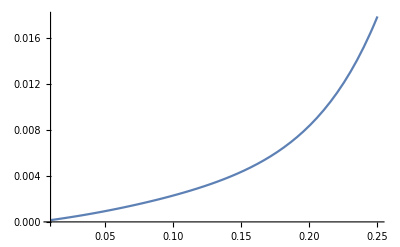

```mathematica
Plot[Abs[ωrdown[2,2,1,x,0.0,0][[1]]^2(0.1275Exp[5.3106 I] *x+1.1882Exp[0.4873 I] x^2+8.2709Exp[3.3895 I] x^3+26.2329Exp[0.1372 I] x^4)],{x,0.01,0.25}]
```

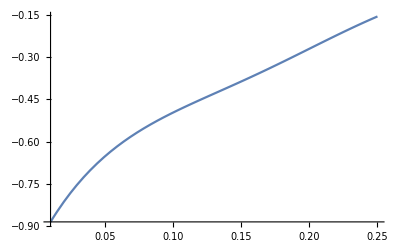

```mathematica
Plot[Arg[ωrdown[2,2,1,x,0.0,0][[1]]^2(0.1275Exp[5.3106 I] *x+1.1882Exp[0.4873 I] x^2+8.2709Exp[3.3895 I] x^3+26.2329Exp[0.1372 I] x^4)],{x,0.01,0.25}]
```

```mathematica
a220/a221
```

4.13618

```mathematica
3.89/0.974
```

3.99384

```mathematica
0.25(-4.0071)
```

-1.00178

### Overtone Fit Functions

```mathematica
DetectConvergence[res_,τ_,OptionsPattern[{"Test"->FindMaximum}]]:=Module[{intres,mins,tmax,t,fits,a,tol,tt,yy,test},

test=OptionValue["Test"];

tmax= 4 * τ;
intres=Interpolation@res;
mins=Quiet[Table[test[intres@t,{t,i}],{i,res[[1,1]]+5,res[[1,1]]+5 +tmax,10}]/.{yy_,tt_}->{t/.tt,yy}];
mins=Select[mins,res[[1,1]]<#[[1]]<res[[-1,1]]&];
SortBy[mins,First]
]
```

```mathematica
Options[OvertoneModel]={"FixExtra"->True,"Fitα"->{},"Fitτ"->{},"Mode"->{2,2},"Varyω"->False,"Mixing"->{False,{2,2}},"ReIm"->False};
OvertoneModel[overtones_,pars_,OptionsPattern[]]:=Block[{ansatz,fixetra,fitα,fitτ,l,m,lm,mm,mixing,mode,modto0,reim,var,varyω,ti,x,y,τs,τsm,α,β,ωm,ωs,ωmτsm,η,χ1,χ2,mixmode},
fixetra=OptionValue["FixExtra"];
fitα=OptionValue["Fitα"];
fitτ=OptionValue["Fitτ"];
mode=OptionValue["Mode"];
varyω=OptionValue["Varyω"];
mixing=OptionValue["Mixing"];
reim=OptionValue["ReIm"];
{lm,mm}=mixing[[2]];

l=mode[[1]];
m=mode[[2]];
{η,χ1,χ2}=pars[[1;;3]];

(* Freqs. & damping times from Vitor *)
ωs=Table[ωlmn[l,m,n,η,χ1,χ2][[1]],{n,0,overtones}];
If[varyω,ωs=Table[If[n>0,var=RandomReal[{0.98,1.02}],var=1];var*ωlmn[l,m,n,η,χ1,χ2][[1]],{n,0,overtones}]];
τs=Table[ωlmn[l,m,n,η,χ1,χ2][[2]],{n,0,overtones}];

ansatz=Sum[If[Not@reim,x=ToExpression["x"<>ToString[n]],x=ToExpression[("x"<>ToString[n]+I "y"<>ToString[n])]]; x Exp[-(t-ti)/(τs[[n+1]](1+ToExpression["β"<>ToString[n]]))] (Cos[ωs[[n+1]](1+ToExpression["α"<>ToString[n]]) (t)]+I Sin[ ωs[[n+1]](1+ToExpression["α"<>ToString[n]]) (t)] ),{n,0,overtones}];
If[mixing[[1]],
ωmτsm=Table[ωlmn[lm,mm,n,η,χ1,χ2],{n,0,overtones}];
ωm=ωmτsm[[All,1]];
τsm=ωmτsm[[All,2]];
ansatz=ansatz+Sum[If[Not@reim,x=ToExpression["xm"<>ToString[n]],x=ToExpression["xm"<>ToString[n]]+I ToExpression["ym"<>ToString[n]]];x Exp[-(t-ti)/(τsm[[n+1]])] (Cos[ωm[[n+1]] (t)]+I Sin[ ωm[[n+1]] (t)] ),{n,0,overtones}]];

modto0=Complement[Table[i,{i,0,overtones}],fitα];
modto0=Table[ToExpression["α"<>ToString[modto0[[i]]]],{i,Length@modto0}];
ansatz=ansatz/.(Table[modto0[[i]]->0,{i,Length@modto0}]);

modto0=Complement[Table[i,{i,0,overtones}],fitτ];
modto0=Table[ToExpression["β"<>ToString[modto0[[i]]]],{i,Length@modto0}];
ansatz=ansatz/.(Table[modto0[[i]]->0,{i,Length@modto0}])
]
```

```mathematica
ComputeBestT0Old[wave_,params_,overtones_,tmaxit_,OptionsPattern[{"NCycles"->6,"Step"->0.1}]]:=Module[{par,cost,ω1,τ1,ω2,τ2,ω3,τ3,ω4,τ4,t0,tf,fit1,waveaux,rsq,rmsq,χ2s,aic,bic,res,ansatz,vars,Astart,A1,ϕ1,A2,ϕ2,A3,ϕ3,
A4,ϕ4,maxres,minres,dist,ncycles,T0,fitdom,frmswq,η,χ1,χ2,posmax,KS,stdσ,step,stepp},

ncycles=OptionValue["NCycles"];
step=OptionValue["Step"];
stepp=Length[Select[wave,#[[1]]≤wave[[1,1]]+step &]];

{η,χ1,χ2}=params;

ω1=ωrdown[2,2,0,η,χ1,χ2][[1]];
τ1=ωrdown[2,2,0,η,χ1,χ2][[2]];
ω2=ωrdown[2,2,1,η,χ1,χ2][[1]];
τ2=ωrdown[2,2,1,η,χ1,χ2][[2]];
ω3=ωrdown[2,2,2,η,χ1,χ2][[1]];
τ3=ωrdown[2,2,2,η,χ1,χ2][[2]];
ω4=0.2515049622;
τ4=0.7051482024;

T0=2π/ω1;
(*Fittaradiale2[t_]:= A1 Exp[-(t-t0)/τ1] Cos[ ω1 (t-t0)+ϕ1 ];*)
posmax=Quiet[Position[wave,_?(#[[1]]≥ tmaxit&)][[1,1]]];
Print["Output -> {fit, rsq, rmsq,χ2,aic,bic,res,t0,dist,fχ2,KS,maxres,minres,fit domain,pars,σ}"];
Table[
Astart= wave[[i,2]];
t0=wave[[i,1]];
tf=wave[[Length@wave,1]];
waveaux=Select[wave,t0≤ #[[1]]<t0+ncycles * T0 &];
fitdom={t0,t0+ncycles * T0};

Which[overtones==1,ansatz= A1 Exp[-(t-t0)/τ1] Cos[ ω1 (t-t0)+ϕ1 ] ; vars={A1, ϕ1};,
      overtones==2,ansatz= A1 Exp[-(t-t0)/τ1] Cos[ ω1 (t-t0)+ϕ1 ] + A2 Exp[-(t-t0)/τ2] Cos[ ω2 (t-t0)+ϕ2 ]; vars={A1,ϕ1,A2,ϕ2};,
      overtones==3,ansatz= A1 Exp[-(t-t0)/τ1] Cos[ ω1 (t-t0)+ϕ1 ] + A2 Exp[-(t-t0)/τ2] Cos[ ω2 (t-t0)+ϕ2 ]+ A3 Exp[-(t-t0)/τ3] Cos[ ω3 (t-t0)+ϕ3 ]; vars={A1,ϕ1,A2,ϕ2,A3,ϕ3};,
      overtones==4,ansatz= A1 Exp[-(t-t0)/τ1] Cos[ ω1 (t-t0)+ϕ1 ] + A2 Exp[-(t-t0)/τ2] Cos[ ω2 (t-t0)+ϕ2 ]+ A3 Exp[-(t-t0)/τ3] Cos[ ω3 (t-t0)+ϕ3 ]+ A4 Exp[-(t-t0)/τ4] Cos[ ω4 (t-t0)+ϕ4 ]; vars={A1,ϕ1,A2,ϕ2,A3,ϕ3,A4,ϕ4};
    ];

fit1=NonlinearModelFit[waveaux,ansatz,vars,t];

rsq=fit1["RSquared"];
res=fit1["FitResiduals"];
rmsq=Sqrt@Mean[res^2];
frmswq=rmsq/Sqrt[Total[wave[[All,2]]^2]];
χ2s=1/Length@res Sum[(res[[i]]^2)/Abs[wave[[i,2]]],{i,Length@res}];
aic=fit1["AIC"];
bic=fit1["BIC"];
maxres=Max[res];
minres=Min[res];
dist=KernelMixtureDistribution[res];
(*KS=PearsonChiSquareTest[res];*)
stdσ=Sqrt[Variance[dist]];
KS=MardiaKurtosisTest[res,"TestStatistic"];
par=fit1["BestFitParameters"];

{fit1,rsq,rmsq,χ2s,aic,bic,res,t0,dist,frmswq,KS,maxres,minres,fitdom,par,stdσ}

,{i,1,posmax,stepp}]
]
```

```mathematica
ComputeBestT0[wave_,params_,overtones_,tmaxit_,OptionsPattern[{"NCycles"->6,"Step"->0.1,"Mode"->{2,2}}]]:=Module[{par,cost,ω1,τ1,ω2,τ2,ω3,τ3,ω4,τ4,ω5,τ5,ω6,τ6,ω7,τ7,t0,tf,fit1,waveaux,rsq,rmsq,χ2s,aic,bic,res,ansatz,vars,Astart,A1,ϕ1,A2,ϕ2,A3,ϕ3,
A4,ϕ4,A5,ϕ5,A6,ϕ6,A7,ϕ7,maxres,minres,dist,ncycles,T0,fitdom,frmswq,η,χ1,χ2,posmax,KS,stdσ,step,stepp,ωs,τs,l,m},

ncycles=OptionValue["NCycles"];
step=OptionValue["Step"];
{l,m}=OptionValue["Mode"];

{η,χ1,χ2}=params;
{ωs,τs}=Transpose@Table[ωrdownV[l,m,n,η,χ1,χ2],{n,0,overtones}];

ansatz=Sum[ToExpression["A"<>ToString[n]] Exp[-(t-t0)/τs[[n+1]]] Cos[ ωs[[n+1]] (t-t0)+ToExpression["ϕ"<>ToString[n]]],{n,0,overtones}];
vars=Flatten@Table[{ToExpression["A"<>ToString[n]],ToExpression["ϕ"<>ToString[n]]},{n,0,overtones}];

T0=2π/ωs[[1]];
(*Fittaradiale2[t_]:= A1 Exp[-(t-t0)/τ1] Cos[ ω1 (t-t0)+ϕ1 ];*)
posmax=Quiet[Position[wave,_?(#[[1]]≥ tmaxit&)][[1,1]]];
Print["Output -> {fit, rsq, rmsq,χ2,aic,bic,res,t0,dist,fχ2,KS,maxres,minres,fit domain,pars,σ}"];
stepp=Length[Select[wave,#[[1]]≤wave[[1,1]]+step &]];
Print[tmaxit];
Table[
Astart= wave[[i,2]];
t0=wave[[i,1]];
tf=wave[[Length@wave,1]];
waveaux=Select[wave,t0≤ #[[1]]<t0+ncycles * T0 &];
fitdom={t0,t0+ncycles * T0};

fit1=NonlinearModelFit[waveaux,ansatz,vars,t,MaxIterations->1000];

rsq=fit1["RSquared"];
res=fit1["FitResiduals"];
rmsq=Sqrt@Mean[res^2];
frmswq=rmsq/Sqrt[Total[wave[[All,2]]^2]];
χ2s=1/Length@res Sum[(res[[i]]^2)/Abs[wave[[i,2]]],{i,Length@res}];
aic=fit1["AIC"];
bic=fit1["BIC"];
maxres=Max[res];
minres=Min[res];
dist=KernelMixtureDistribution[res];
(*KS=PearsonChiSquareTest[res];*)
stdσ=Sqrt[Variance[dist]];
KS=MardiaKurtosisTest[res,"TestStatistic"];
par=fit1["BestFitParameters"];

{fit1,rsq,rmsq,χ2s,aic,bic,res,t0,dist,frmswq,KS,maxres,minres,fitdom,par,stdσ}

,{i,1,posmax,stepp}]
]
```

```mathematica
ComputeBestT0v2[wave_,params_,overtones_,tmaxit_,OptionsPattern[{"NCycles"->6,"Step"->0.1,"Mode"->{2,2}}]]:=Module[{par,cost,ω1,τ1,ω2,τ2,ω3,τ3,ω4,τ4,ω5,τ5,ω6,τ6,ω7,τ7,t0,tf,fit1,waveaux,rsq,rmsq,χ2s,aic,bic,res,ansatz,vars,Astart,A1,ϕ1,A2,ϕ2,A3,ϕ3,
A4,ϕ4,A5,ϕ5,A6,ϕ6,A7,ϕ7,maxres,minres,dist,ncycles,T0,fitdom,frmswq,η,χ1,χ2,posmax,KS,stdσ,step,stepp,ωs,τs,l,m},

ncycles=OptionValue["NCycles"];
step=OptionValue["Step"];
{l,m}=OptionValue["Mode"];

{η,χ1,χ2}=params;
{ωs,τs}=Transpose@Table[ωrdownV[l,m,n,η,χ1,χ2],{n,0,overtones}];

ansatz=Sum[ToExpression["A"<>ToString[n]] Exp[-(t-t0)/τs[[n+1]]] Cos[ ωs[[n+1]] (t-t0)+ToExpression["ϕ"<>ToString[n]]],{n,0,overtones}];
vars=Flatten@Table[{ToExpression["A"<>ToString[n]],ToExpression["ϕ"<>ToString[n]]},{n,0,overtones}];

T0=2π/ωs[[1]];
(*Fittaradiale2[t_]:= A1 Exp[-(t-t0)/τ1] Cos[ ω1 (t-t0)+ϕ1 ];*)
posmax=Quiet[Position[wave,_?(#[[1]]≥ tmaxit&)][[1,1]]];
Print["Output -> {fit, rsq, rmsq,χ2,aic,bic,res,t0,dist,fχ2,KS,maxres,minres,fit domain,pars,σ}"];
stepp=Length[Select[wave,#[[1]]≤wave[[1,1]]+step &]];

Table[
Astart= wave[[i,2]];
t0=wave[[i,1]];
tf=wave[[Length@wave,1]];
waveaux=Select[wave,t0≤ #[[1]]<tmaxit &];
fitdom={t0,t0+ncycles * T0};

fit1=NonlinearModelFit[waveaux,ansatz,vars,t,MaxIterations->1000];

rsq=fit1["RSquared"];
res=fit1["FitResiduals"];
rmsq=Sqrt@Mean[res^2];
frmswq=rmsq/Sqrt[Total[wave[[All,2]]^2]];
χ2s=1/Length@res Sum[(res[[i]]^2)/Abs[wave[[i,2]]],{i,Length@res}];
aic=fit1["AIC"];
aic = aic + (2*Length@vars(Length@vars+1))/(Length@waveaux - Length@vars -1);
bic=fit1["BIC"];
maxres=Max[res];
minres=Min[res];
dist=KernelMixtureDistribution[res];
(*KS=PearsonChiSquareTest[res];*)
stdσ=Sqrt[Variance[dist]];
KS=MardiaKurtosisTest[res,"TestStatistic"];
par=fit1["BestFitParameters"];

{fit1,rsq,rmsq,χ2s,aic,bic,res,t0,dist,frmswq,KS,maxres,minres,fitdom,par,stdσ}

,{i,1,Round[posmax/2],stepp}]
]
```

```mathematica
Options[CNMinimize]={"Method"->Automatic};
CNMinimize[data_,ansatz_,vars_,{x_,xlist_},OptionsPattern[]]:=Module[{likelihood,ansatzlist,method},
method=OptionValue["Method"];

ansatzlist=ansatz/.x->xlist;
likelihood=Total[(Re[ansatzlist-data]^2+Im[ansatzlist-data]^2)];
NMinimize[likelihood,vars,Method->method]
];
```

## Load data

```mathematica
join=False;
sxsdir="/Users/xisco/SXS";(
sxsdirs=Drop[Select[FileNames["*",sxsdir],DirectoryQ[#]&],-1])//TableForm
joincase=
Drop[If[join,Join[sxsdirs,{"/Users/xisco/SXS/d13.0_q8.0_s0_0_-0.5_s0","/Users/xisco/SXS/BBH_SKS_d14.3_q1.22_sA_0_0_0.330_sB_0_0_-0.440"}],sxsdirs],-1]
```

/Users/xisco/SXS/0031
/Users/xisco/SXS/019
/Users/xisco/SXS/BBH_CFMS_d11.4_q9_sA_0_0_0_sB_0_0_0
/Users/xisco/SXS/BBH_CFMS_d12.2_q7_sA_0_0_0_sB_0_0_0
/Users/xisco/SXS/BBH_CFMS_d12.6_q4_sA_0_0_0_sB_0_0_0
/Users/xisco/SXS/BBH_CFMS_d13_q10_sA_0_0_0_sB_0_0_0
/Users/xisco/SXS/BBH_CFMS_d15.9_q3.50_sA_0_0_0_sB_0_0_0
/Users/xisco/SXS/BBH_SKS_d12.7_q1.25_sA_0_0_0_sB_0_0_0
/Users/xisco/SXS/BBH_SKS_d14.3_q1.22_sA_0_0_0.330_sB_0_0_-0.440
/Users/xisco/SXS/BBH_SKS_d14_q6_sA_0_0_0_sB_0_0_0
/Users/xisco/SXS/BBH_SKS_d15.2_q4_sA_0_0_0_sB_0_0_0
/Users/xisco/SXS/d13.0_q8.0_s0_0_-0.5_s0
/Users/xisco/SXS/d13_q2_sA_0_0_0_sB_0_0_0
/Users/xisco/SXS/d13_q6_sA_0_0_0_sB_0_0_0
/Users/xisco/SXS/d14.0_q3.0_s0_0_0_s0_0_0
/Users/xisco/SXS/d18.0_q1.0_s0_0_0_s0_0_0F1
/Users/xisco/SXS/d18.0_q1.5_s0_0_0_s0_0_0
/Users/xisco/SXS/data

{/Users/xisco/SXS/0031,/Users/xisco/SXS/019,/Users/xisco/SXS/BBH_CFMS_d11.4_q9_sA_0_0_0_sB_0_0_0,/Users/xisco/SXS/BBH_CFMS_d12.2_q7_sA_0_0_0_sB_0_0_0,/Users/xisco/SXS/BBH_CFMS_d12.6_q4_sA_0_0_0_sB_0_0_0,/Users/xisco/SXS/BBH_CFMS_d13_q10_sA_0_0_0_sB_0_0_0,/Users/xisco/SXS/BBH_CFMS_d15.9_q3.50_sA_0_0_0_sB_0_0_0,/Users/xisco/SXS/BBH_SKS_d12.7_q1.25_sA_0_0_0_sB_0_0_0,/Users/xisco/SXS/BBH_SKS_d14.3_q1.22_sA_0_0_0.330_sB_0_0_-0.440,/Users/xisco/SXS/BBH_SKS_d14_q6_sA_0_0_0_sB_0_0_0,/Users/xisco/SXS/BBH_SKS_d15.2_q4_sA_0_0_0_sB_0_0_0,/Users/xisco/SXS/d13.0_q8.0_s0_0_-0.5_s0,/Users/xisco/SXS/d13_q2_sA_0_0_0_sB_0_0_0,/Users/xisco/SXS/d13_q6_sA_0_0_0_sB_0_0_0,/Users/xisco/SXS/d14.0_q3.0_s0_0_0_s0_0_0,/Users/xisco/SXS/d18.0_q1.0_s0_0_0_s0_0_0F1,/Users/xisco/SXS/d18.0_q1.5_s0_0_0_s0_0_0}

```mathematica
(mysxscase=SXSParClassification[sxsdirs,{{"Non-Precessing"},{"χ1","#<0.01"},{"χ2","#<0.01"}}][[1;;-3]]);
If[join,mysxscase=Join[sxsdirs,{"/Users/xisco/SXS/d13.0_q8.0_s0_0_-0.5_s0","/Users/xisco/SXS/BBH_SKS_d14.3_q1.22_sA_0_0_0.330_sB_0_0_-0.440"}]];
mysxscase//TableForm
modes={{2,2},{2,1},{3,3},{3,2}}
```

Classification Input Variables. Examples: {{'MassRatio', '0.99<#<1.1'}},{{'Distance', '#>16'}},{{'Orbits', '#>25'}},{{'Precessing'}},
{{'Non-Precessing'}},{{'High-Spin'}},{{'χeff','#>0.6'}},{{'χ1','#>0.6'}},{{'χ2','#>0.6'}},{{'Unequal'}}

Take care! Some of the sxs file names are not consistent with the metadata files

The spin definition is consitent with 'initial-spin' values and not relaxed ones

The mass definition is consitent with 'initial-mass' values and not relaxed ones

/Users/xisco/SXS/d18.0_q1.0_s0_0_0_s0_0_0F1
/Users/xisco/SXS/BBH_SKS_d12.7_q1.25_sA_0_0_0_sB_0_0_0
/Users/xisco/SXS/d18.0_q1.5_s0_0_0_s0_0_0
/Users/xisco/SXS/d13_q2_sA_0_0_0_sB_0_0_0
/Users/xisco/SXS/d14.0_q3.0_s0_0_0_s0_0_0
/Users/xisco/SXS/BBH_CFMS_d15.9_q3.50_sA_0_0_0_sB_0_0_0
/Users/xisco/SXS/BBH_CFMS_d12.6_q4_sA_0_0_0_sB_0_0_0
/Users/xisco/SXS/BBH_SKS_d15.2_q4_sA_0_0_0_sB_0_0_0
/Users/xisco/SXS/BBH_SKS_d14_q6_sA_0_0_0_sB_0_0_0
/Users/xisco/SXS/d13_q6_sA_0_0_0_sB_0_0_0
/Users/xisco/SXS/BBH_CFMS_d12.2_q7_sA_0_0_0_sB_0_0_0

{{2,2},{2,1},{3,3},{3,2}}

```mathematica
mysxscaserh=Table[FileNames["*rhO*",mysxscase[[i]],2][[-1]],{i,Length@mysxscase}]
mysxscasemetafile=Flatten[Table[FileNames["metadata.txt",FileNameDrop[mysxscaserh[[i]],-2],2],{i,Length@mysxscaserh}]]
```

{/Users/xisco/SXS/d18.0_q1.0_s0_0_0_s0_0_0F1/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/BBH_SKS_d12.7_q1.25_sA_0_0_0_sB_0_0_0/Lev3/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/d18.0_q1.5_s0_0_0_s0_0_0/Lev6/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/d13_q2_sA_0_0_0_sB_0_0_0/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/d14.0_q3.0_s0_0_0_s0_0_0/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/BBH_CFMS_d15.9_q3.50_sA_0_0_0_sB_0_0_0/Lev4/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/BBH_CFMS_d12.6_q4_sA_0_0_0_sB_0_0_0/Lev4/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/BBH_SKS_d15.2_q4_sA_0_0_0_sB_0_0_0/Lev4/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/BBH_SKS_d14_q6_sA_0_0_0_sB_0_0_0/Lev4/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/d13_q6_sA_0_0_0_sB_0_0_0/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5,/Users/xisco/SXS/BBH_CFMS_d12.2_q7_sA_0_0_0_sB_0_0_0/Lev5/rhOverM_Asymptotic_GeometricUnits_CoM.h5}

{/Users/xisco/SXS/d18.0_q1.0_s0_0_0_s0_0_0F1/Lev5/metadata.txt,/Users/xisco/SXS/BBH_SKS_d12.7_q1.25_sA_0_0_0_sB_0_0_0/Lev3/metadata.txt,/Users/xisco/SXS/d18.0_q1.5_s0_0_0_s0_0_0/Lev6/metadata.txt,/Users/xisco/SXS/d13_q2_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/d14.0_q3.0_s0_0_0_s0_0_0/Lev5/metadata.txt,/Users/xisco/SXS/BBH_CFMS_d15.9_q3.50_sA_0_0_0_sB_0_0_0/Lev4/metadata.txt,/Users/xisco/SXS/BBH_CFMS_d12.6_q4_sA_0_0_0_sB_0_0_0/metadata.txt,/Users/xisco/SXS/BBH_SKS_d15.2_q4_sA_0_0_0_sB_0_0_0/Lev2/metadata.txt,/Users/xisco/SXS/BBH_SKS_d14_q6_sA_0_0_0_sB_0_0_0/Lev4/metadata.txt,/Users/xisco/SXS/d13_q6_sA_0_0_0_sB_0_0_0/Lev5/metadata.txt,/Users/xisco/SXS/BBH_CFMS_d12.2_q7_sA_0_0_0_sB_0_0_0/Lev5/metadata.txt}

```mathematica
mysxscasemetadata=SXSMetaFilesToRules/@mysxscasemetafile;
Print["tag = ",tag=StringReplace[("alternative-names"/.mysxscasemetadata)[[All,-1]],":BBH"->""]]
Print["mass1 = ",mass1=Flatten[("initial-mass1"/.mysxscasemetadata),1]]
Print["mass2 = ",mass2=Flatten[("initial-mass2"/.mysxscasemetadata),1]]
Print["χ1 = ",χ1=Chop[(("initial-dimensionless-spin1"/.mysxscasemetadata)[[All,-1]])]]
Print["χ2 = ",χ2=Chop[(("initial-dimensionless-spin2"/.mysxscasemetadata)[[All,-1]])]]
Print["m1/m2 = ",q=mass1/mass2]
Print["m1·m2 = ",η=q/(1+q)^2*1.]
Print["af = ",af=("remnant-dimensionless-spin"/.mysxscasemetadata)[[All,-1]]]
Print["mf = ",mf=("remnant-mass"/.mysxscasemetadata)[[All,-1]]]
Print["kick = ", vr=("remnant-velocity"/.mysxscasemetadata) ]
```

tag = {SXS:0070,SXS:1143,SXS:0007,SXS:0169,SXS:0030,SXS:0294,SXS:0182,SXS:1220,SXS:0181,SXS:0166,SXS:0298}

mass1 = {0.5,0.555556,0.6,0.666667,0.75,0.777778,0.8,0.8,0.857144,0.857143,0.875}

mass2 = {0.5,0.444444,0.4,0.333333,0.25,0.222222,0.2,0.2,0.142858,0.142857,0.125}

χ1 = {6.41852×10^-9,-8.57368×10^-8,1.25703×10^-9,3.13694×10^-8,1.16911×10^-9,3.53722×10^-9,1.54966×10^-8,-1.7059×10^-9,-2.75916×10^-8,9.18943×10^-9,0}

χ2 = {1.8664×10^-10,-9.04577×10^-9,0,6.97374×10^-10,4.36374×10^-10,8.81043×10^-10,-1.36497×10^-8,-1.64615×10^-8,-5.77306×10^-8,9.15205×10^-9,0}

m1/m2 = {1.,1.25,1.5,2.,3.,3.5,4.,4.,5.99997,6.,7.}

m1·m2 = {0.25,0.246914,0.24,0.222222,0.1875,0.17284,0.16,0.16,0.122449,0.122449,0.109375}

af = {0.68646,0.679537,0.664091,0.623439,0.540644,0.504184,0.471647,0.471805,0.372483,0.372452,0.336515}

mf = {0.951609,0.952754,0.95527,0.961246,0.971213,0.974932,0.977899,0.977701,0.98545,0.985471,0.987715}

kick = {{1.88811×10^-9,-8.02529×10^-10,3.64569×10^-9},{0.000171012,-0.0000928392,2.06307×10^-8},{0.000339656,-4.20179×10^-6,3.4005×10^-9},{-0.000457766,0.000212721,1.85904×10^-9},{0.000494583,0.000297346,6.2481×10^-10},{0.000103773,-0.00055965,1.05747×10^-9},{-0.00013705,0.000518622,-3.88873×10^-9},{0.000542523,0.000276993,2.64841×10^-6},{0.000240054,0.000353424,-3.17143×10^-9},{0.0000181846,0.000391503,8.47221×10^-11},{-0.000236042,0.000217238,4.55994×10^-9}}

```mathematica
sxsrhs=Conjugate/@GetAsymptoticMultiMode[#,2,modes,"ReSample"->True]&/@mysxscaserh;
```

```mathematica
tmax=TimeOfMaximum/@(sxsrhs[[All,1]])
```

{9520.74,2303.99,9872.23,3729.24,4463.23,8155.81,3327.46,7192.71,6587.58,4891.72,4143.46}

```mathematica
(* We eliminate SXS:0070 (i=1),  SXS:0007 (i=3) for inaccuracies *)
```

```mathematica
(* Fix this later *)
dropindex={3};
Print["tag = ",tag=Drop[tag,dropindex]]
Print["mass1 = ",mass1=Drop[mass1,dropindex]]
Print["mass2 = ",mass2=Drop[mass2,dropindex]]
Print["χ1 = ",χ1=Drop[χ1,dropindex]]
Print["χ2 = ",χ2=Drop[χ2,dropindex]]
Print["m1/m2 = ",q=Drop[q,dropindex]]
Print["m1·m2 = ",η=Drop[η,dropindex]]
Print["af = ",af=Drop[af,dropindex]]
Print["mf = ",mf=Drop[mf,dropindex]]
Print["kick = ",vr=Drop[vr,dropindex] ]
```

tag = {SXS:0070,SXS:1143,SXS:0169,SXS:0030,SXS:0294,SXS:0182,SXS:1220,SXS:0181,SXS:0166,SXS:0298}

mass1 = {0.5,0.555556,0.666667,0.75,0.777778,0.8,0.8,0.857144,0.857143,0.875}

mass2 = {0.5,0.444444,0.333333,0.25,0.222222,0.2,0.2,0.142858,0.142857,0.125}

χ1 = {6.41852×10^-9,-8.57368×10^-8,3.13694×10^-8,1.16911×10^-9,3.53722×10^-9,1.54966×10^-8,-1.7059×10^-9,-2.75916×10^-8,9.18943×10^-9,0}

χ2 = {1.8664×10^-10,-9.04577×10^-9,6.97374×10^-10,4.36374×10^-10,8.81043×10^-10,-1.36497×10^-8,-1.64615×10^-8,-5.77306×10^-8,9.15205×10^-9,0}

m1/m2 = {1.,1.25,2.,3.,3.5,4.,4.,5.99997,6.,7.}

m1·m2 = {0.25,0.246914,0.222222,0.1875,0.17284,0.16,0.16,0.122449,0.122449,0.109375}

af = {0.68646,0.679537,0.623439,0.540644,0.504184,0.471647,0.471805,0.372483,0.372452,0.336515}

mf = {0.951609,0.952754,0.961246,0.971213,0.974932,0.977899,0.977701,0.98545,0.985471,0.987715}

kick = {{1.88811×10^-9,-8.02529×10^-10,3.64569×10^-9},{0.000171012,-0.0000928392,2.06307×10^-8},{-0.000457766,0.000212721,1.85904×10^-9},{0.000494583,0.000297346,6.2481×10^-10},{0.000103773,-0.00055965,1.05747×10^-9},{-0.00013705,0.000518622,-3.88873×10^-9},{0.000542523,0.000276993,2.64841×10^-6},{0.000240054,0.000353424,-3.17143×10^-9},{0.0000181846,0.000391503,8.47221×10^-11},{-0.000236042,0.000217238,4.55994×10^-9}}

```mathematica
ϕq=ArcTan[vr[[All,2]]/vr[[All,1]]]
```

{-0.401907,-0.497362,-0.435006,0.541305,-1.38745,-1.31244,0.472064,0.97415,1.52438,-0.743935}

```mathematica
sxsrhs=Drop[sxsrhs,dropindex];
```

```mathematica
tmax=Drop[tmax,dropindex]
```

{9520.74,2303.99,3729.24,4463.23,8155.81,3327.46,7192.71,6587.58,4891.72,4143.46}

```mathematica
(* Structure of ws: 1 index-> tag, 2 index -> n , 3 index -> lm , 4 index -> ω τ*)
```

```mathematica
ws22=Table[{ωlmn[2,2,n,η[[ind]],χ1[[ind]],χ2[[ind]]]},{n,0,6},{ind,Length@tag}];
ws21=Table[{ωlmn[2,1,n,η[[ind]],χ1[[ind]],χ2[[ind]]]},{n,0,6},{ind,Length@tag}];
ws33=Table[{ωlmn[3,3,n,η[[ind]],χ1[[ind]],χ2[[ind]]]},{n,0,6},{ind,Length@tag}];
```

## Fits Non-Spinning (lm)

#### n=0

```mathematica
<<PNStrain.m
```

```mathematica
DefineYlms[2,4];
```

```mathematica
Ylm[2,2]
```

1/2 ⅇ^(2 ⅈ yphi) √(5/π) Cos[ytheta/2]^4

```mathematica
tfit=10;
```

```mathematica
(* Remember that t0lm varies !*)
```

```mathematica
(* Here start the α0,α1 contours*)
ansall=Table[
t0[index]=tmax[[index]];
mysxscase22modeRD[index]=Table[Select[sxsrhs[[index,i]],#[[1]]≥ tmax[[index]]&],{i,Length@modes}];
ans=Table[OvertoneModel[0,{η[[index]],χ1[[index]],χ2[[index]]},"Fitα"->{},"Mode"->modes[[i]]]/.ti->(tfit),{i,Length@modes}],{index,1,Length@tag}];
```

```mathematica
val022=Table[(Select[Arg0DStructs[mysxscase22modeRD[i][[1]]],#[[1]]≥ tmax[[i]]+tfit&,1])[[1,2]],{i,Length@tag}];
val021=Table[(Select[Arg0DStructs[mysxscase22modeRD[i][[2]]],#[[1]]≥ tmax[[i]]+tfit&,1])[[1,2]],{i,Length@tag}];
val033=Table[(Select[Arg0DStructs[mysxscase22modeRD[i][[3]]],#[[1]]≥ tmax[[i]]+tfit&,1])[[1,2]],{i,Length@tag}];
```

```mathematica
phs0={val022,val021,val033}
```

{{5.21523,3.77056,4.06827,5.85542,2.04401,2.22446,4.80165,0.361813,1.54004,3.29644},{1.30762,0.444318,3.74426,1.41171,5.79803,2.73592,0.856108,1.73734,2.34928,3.22479},{3.05762,9.53213,6.81621,6.29361,6.84283,3.94551,4.66418,7.36861,2.86942,5.49252}}

```mathematica
mysxscase22modeRD0sh=Table[mysxscase22modeRD[index][[j]]/.{xx_,yy_}->{xx-tmax[[index]],yy Exp[-I phs0[[j,index]]]},{index,Length@tag},{j,Length@modes}];
```

```mathematica
Chop@Mod[Table[Select[Arg0DStructs@mysxscase22modeRD0sh[[i,1]],#[[1]]≥ 10&,1][[1,2]],{i,Length@tag}],2π]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
t0ampsdataall=Table[
data=Select[mysxscase22modeRD0sh[[index,j]],#[[1]]≥i&];

(*ansl=ansall[[index,j]]Exp[I modes[[j,2]](ϕq[[index]]+phs0[[j,index]]/modes[[j,2]])];*)


ansl=ansall[[index,j]];
cfit=NonlinearModelFit[data,ansl,{x0},t];
amps={x0}/.cfit["BestFitParameters"];

{i,amps[[1]]},{index,Length@tag},{j,Length@modes},{i,0,100}];
```

```mathematica
amps15=Table[Select[(Abs/@(t0ampsdataall[[i,j]])),#[[1]]≥tfit&,1][[1,2]],{i,Length@tag},{j,Length@modes}]
```

{{0.354353,5.96722×10^-9,2.21452×10^-8},{0.358086,0.0142991,0.0209108},{0.313188,0.0385913,0.053328},{0.269458,0.0514114,0.064762},{0.243284,0.052642,0.0677696},{0.225645,0.0529913,0.0639304},{0.228118,0.0537946,0.0646426},{0.173752,0.0508678,0.0563134},{0.172794,0.0504103,0.0562363},{0.153012,0.0470737,0.0516644}}

```mathematica
phse15=Table[Select[(Arg0DStructs@(t0ampsdataall[[i,j]])),#[[1]]≥10&,1][[1,2]],{i,Length@tag},{j,Length@modes}]
```

{{0.488667,-3.20737,-3.33461},{0.515815,1.20396,-2.84456},{0.835107,1.38482,-2.36798},{1.18378,1.56143,-1.82653},{1.32645,1.64516,-1.59977},{1.43498,1.70112,-1.4608},{1.42961,1.69192,-1.47246},{1.71838,1.84418,-1.02545},{1.71955,1.84228,-1.02912},{1.81145,1.89391,-0.888748}}

```mathematica
fun220=Normal@NonlinearModelFit[Transpose[{q/(q+1)^2,Mod[phse15[[All,1]],2π]}],A0 eta (x0  +x1 eta+x2 eta^2 ),{A0,x0,x1},eta]
```

6.56644 (3.69187 eta-13.8639 eta^2)

```mathematica
fun220=Normal@NonlinearModelFit[Transpose[{q/(q+1)^2,Mod[phse15[[All,1]],2π]}],A0 eta (x0 +x1 eta)+c0,{A0,c0,x0,x1,x2,x3},eta]
```

2.19719+1.83869 (-0.571621-12.5931 eta) eta

```mathematica
fun221=Normal@NonlinearModelFit[Drop[Transpose[{q/(q+1)^2,Mod[phse15[[All,2]],2π]}],1],A0 eta (x0 +x1 eta)+c0,{A0,c0,x0,x1,x2,x3},eta]
```

2.05547+1.16946 (-0.0268449-11.7288 eta) eta

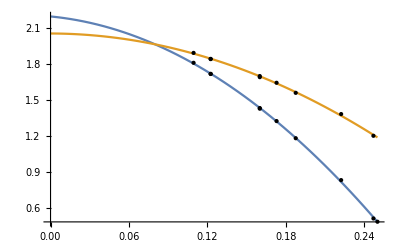

```mathematica
Plot[{fun220,fun221},{eta,0.,0.25},Epilog->{{Point[Transpose[{q/(q+1)^2,Mod[phse15[[All,1]],2π]}]]},{Point[Transpose[{q/(q+1)^2,Mod[phse15[[All,2]],2π]}]]}}]
```

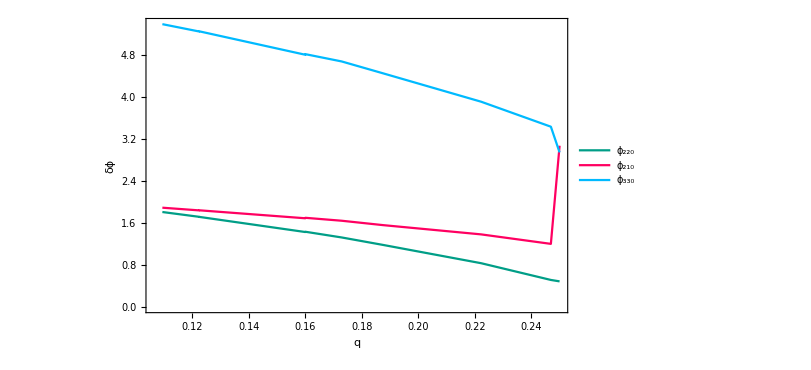

```mathematica
lp=ListLinePlot[{Transpose[{q/(q+1)^2,Mod[phse15[[All,1]],2π]}],Transpose[{q/(q+1)^2,Mod[phse15[[All,2]],2π]}],Transpose[{q/(q+1)^2,Mod[phse15[[All,3]],2π]}]},PlotStyle->colors,Frame->True,PlotLegends->Placed[{"ϕ_220","ϕ_210","ϕ_330"},{0.85,0.8}],FrameLabel->{"q","δϕ"},ImageSize->600,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full]
```

#### n=0 (with 32)

```mathematica
(* Here start the α0,α1 contours*)
ansall=Table[
t0[index]=tmax[[index]];
mysxscase22modeRD[index]=Table[Select[sxsrhs[[index,i]],#[[1]]≥ tmax[[index]]&],{i,Length@modes}];
ans=Table[If[modes[[i,1]]==3&&modes[[i,2]]==2,mix=True,mix=False];OvertoneModel[0,{η[[index]],χ1[[index]],χ2[[index]]},"Fitα"->{},"Mode"->modes[[i]],"Mixing"->{mix,{2,2}}]/.ti->(tfit),{i,Length@modes}],{index,1,Length@tag}];
```

```mathematica
val022=Table[(Select[Arg0DStructs[mysxscase22modeRD[i][[1]]],#[[1]]≥ tmax[[i]]+tfit&,1])[[1,2]],{i,Length@tag}];
val021=Table[(Select[Arg0DStructs[mysxscase22modeRD[i][[2]]],#[[1]]≥ tmax[[i]]+tfit&,1])[[1,2]],{i,Length@tag}];
val033=Table[(Select[Arg0DStructs[mysxscase22modeRD[i][[3]]],#[[1]]≥ tmax[[i]]+tfit&,1])[[1,2]],{i,Length@tag}];
val032=Table[(Select[Arg0DStructs[mysxscase22modeRD[i][[4]]],#[[1]]≥ tmax[[i]]+tfit&,1])[[1,2]],{i,Length@tag}];
```

```mathematica
phs0={val022,val021,val033,val032}
```

{{10.3195,8.81611,8.9143,10.4083,6.50704,6.59793,9.16649,4.49635,5.67482,7.3584},{1.09319,4.59637,7.78449,5.261,9.59959,6.48011,4.58937,5.32976,5.93391,6.77175},{7.44781,17.5777,14.5474,13.5872,14.0059,10.9375,11.6362,13.9896,9.47113,11.9764},{10.6522,9.09747,9.01573,10.0126,5.73502,11.7526,14.283,8.75266,9.95516,11.5029}}

```mathematica
mysxscase22modeRD0sh=Table[mysxscase22modeRD[index][[j]]/.{xx_,yy_}->{xx-tmax[[index]],yy Exp[-I phs0[[j,index]]]},{index,Length@tag},{j,Length@modes}];
```

```mathematica
Chop@Mod[Table[Select[Arg0DStructs@mysxscase22modeRD0sh[[i,1]],#[[1]]≥ 10&,1][[1,2]],{i,Length@tag}],2π]
```

{1.17893,1.23763,1.43716,1.73035,1.82016,1.90971,1.91834,2.14865,2.1484,2.22123}

```mathematica
t0ampsdataall=Table[
data=Select[mysxscase22modeRD0sh[[index,j]],#[[1]]≥i&];
ansl=ansall[[index,j]];
cfit=NonlinearModelFit[data,ansl,{x0,xm0},t];
amps={x0,xm0}/.cfit["BestFitParameters"];

{i,amps},{index,Length@tag},{j,Length@modes},{i,0,100}];
```

```mathematica
cfitn=Normal@cfit
```

(0.00119393+0.000185021 ⅈ) ⅇ^(0.0885456 (20-t)) (Cos[0.431883 t]+ⅈ Sin[0.431883 t])+(0.00282862-0.00585014 ⅈ) ⅇ^(0.092372 (20-t)) (Cos[0.663431 t]+ⅈ Sin[0.663431 t])

```mathematica
t0ampsdataall=Table[
data=Select[mysxscase22modeRD0sh[[index,j]],#[[1]]≥i&];
ansl=ansall[[index,j]];
cfit=NonlinearModelFit[data,ansl,{x0,xm0},t];
amps={x0,xm0}/.cfit["BestFitParameters"];

{i,amps},{index,Length@tag},{j,Length@modes},{i,20,20}];
```

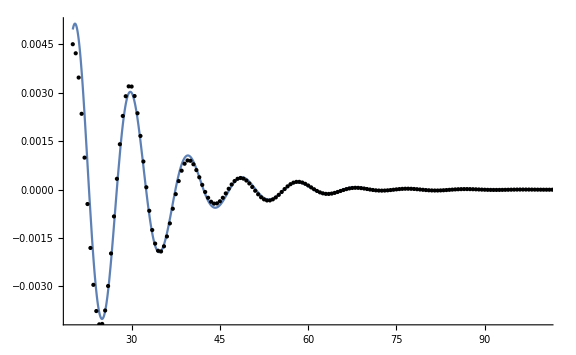

```mathematica
Plot[Re@cfitn,{t,20,100},PlotRange->All,Epilog->Point[Re@data],ImageSize->Large]
```

```mathematica
amps15=Table[Select[(Abs/@(t0ampsdataall[[i,j]])),#[[1]]≥tfit&,1][[1,2]],{i,Length@tag},{j,Length@modes}]
```

{{{0.169483,0.},{8.23588×10^-9,0.},{4.66485×10^-9,0.},{0.00512717,0.0112253}},{{0.172758,0.},{0.00725114,0.},{0.0107376,0.},{0.00455263,0.0113755}},{{0.148158,0.},{0.0192864,0.},{0.0263105,0.},{0.00122662,0.00874054}},{{0.127567,0.},{0.0260724,0.},{0.0306151,0.},{0.00271061,0.00628786}},{{0.114167,0.},{0.0266051,0.},{0.0330446,0.},{0.00384563,0.0051713}},{{0.105869,0.},{0.0267417,0.},{0.0307487,0.},{0.00454608,0.00445927}},{{0.107512,0.},{0.0273922,0.},{0.0312021,0.},{0.0046904,0.00454592}},{{0.0816708,0.},{0.0259929,0.},{0.0269202,0.},{0.00601754,0.0027646}},{{0.0812542,0.},{0.0256631,0.},{0.0267827,0.},{0.00592909,0.0026818}},{{0.0717676,0.},{0.0239404,0.},{0.0244972,0.},{0.00591673,0.00212102}}}

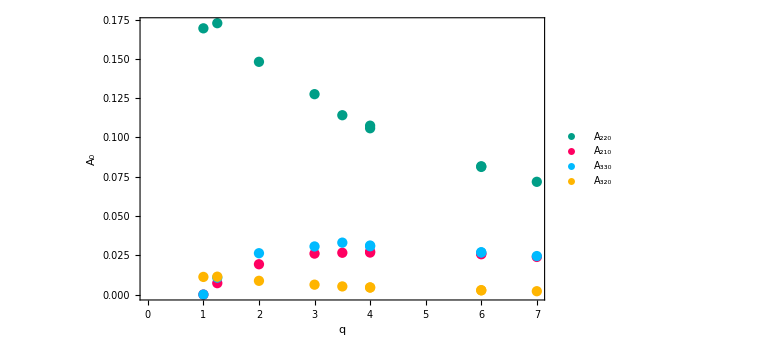

```mathematica
lp=ListPlot[{Transpose[{q,amps15[[All,1,1]]}],Transpose[{q,amps15[[All,2,1]]}],Transpose[{q,amps15[[All,3,1]]}],Transpose[{q,amps15[[All,4,2]]}]},PlotStyle->colors,Frame->True,PlotLegends->Placed[{"A_220","A_210","A_330","A_320"},{0.85,0.8}],FrameLabel->{"q","A_0"},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full]
```

```mathematica
mus=Table[ModeMixingFitCoeffSY[q[[i]]/(q[[i]]+1)^2,χ1[[i]],χ2[[i]],2,2,3,0],{i,Length@q}]
```

{0.097101+0.00899369 ⅈ,0.0958112+0.00895285 ⅈ,0.0721211+0.00771306 ⅈ,0.06647+0.0073044 ⅈ,0.0615404+0.00692141 ⅈ,0.0615404+0.00692141 ⅈ,0.0471044+0.00568477 ⅈ,0.0471042+0.00568475 ⅈ,0.0420416+0.00521625 ⅈ}

```mathematica
mus=ModeMixingFitCoeffSY[q/(q+1)^2,0,0,2,3,2,0]
```

{-0.0675039-0.0111402 ⅈ,-0.0665251-0.0110391 ⅈ,-0.0590183-0.0101896 ⅈ,-0.0490585-0.0089017 ⅈ,-0.0449507-0.00833031 ⅈ,-0.0413729-0.00781682 ⅈ,-0.0413729-0.00781682 ⅈ,-0.0309508-0.0062421 ⅈ,-0.0309506-0.00624208 ⅈ,-0.0273339-0.0056665 ⅈ}

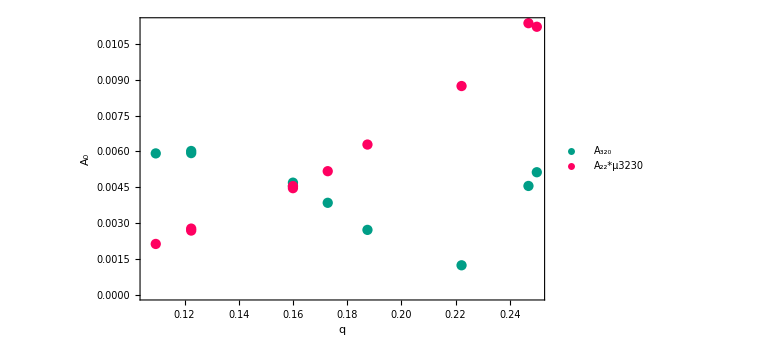
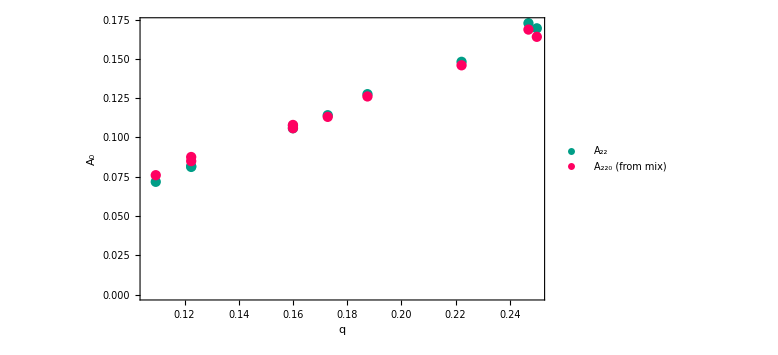

```mathematica
{ListPlot[{Transpose[{q/(q+1)^2,Abs[amps15[[All,4,1]]]}],Transpose[{q/(q+1)^2,Abs[amps15[[All,4,2]]]}]},PlotStyle->colors,Frame->True,PlotLegends->Placed[{"A_320","A_22*μ3230"},{0.15,0.8}],FrameLabel->{"q","A_0"},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full],

ListPlot[{Transpose[{q/(q+1)^2,Abs[amps15[[All,1,1]]]}],Transpose[{q/(q+1)^2,Abs[amps15[[All,4,2]]/((-1)^(-1)mus)]}]},PlotStyle->colors,Frame->True,PlotLegends->Placed[{"A_22","A_220 (from mix)"},{0.15,0.8}],FrameLabel->{"q","A_0"},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full]}
```

```mathematica
Export["/Users/xisco/Work/INFN/Work/Rdown/plotsV2/AmpFitQ.pdf",lp]
```

/Users/xisco/Work/INFN/Work/Rdown/plotsV2/AmpFitQ.pdf

```mathematica
phse15=Table[Select[(Arg0DStructs@(Transpose[{t0ampsdataall[[i,j,All,1]],t0ampsdataall[[i,j,All,2,1]]}])),#[[1]]≥tfit&,1][[1,2]],{i,Length@tag},{j,Length@modes}]
```

{{1.43333,-3.05641,-1.32451,-2.70714},{1.51273,3.00955,1.32901,-2.72279},{2.07279,-2.95466,2.17311,-2.46239},{2.7327,-2.58999,-3.10733,2.61755},{2.98107,-2.44381,-2.67017,-3.03962},{-3.09584,-2.3316,-2.41154,-2.61448},{-3.09659,-2.3337,-2.409,-2.62651},{-2.5573,-2.03174,-1.5741,-1.34727},{-2.55771,-2.0313,-1.57675,-1.35266},{-2.38671,-1.93778,-1.31267,-1.05931}}

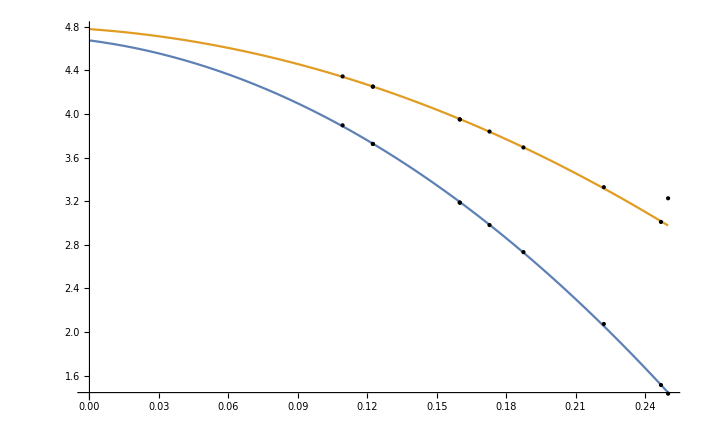

```mathematica
Plot[{fun220,fun221},{eta,0.,0.25},Epilog->{{Point[Transpose[{q/(q+1)^2,Mod[phse15[[All,1]],2π]}]]},{Point[Transpose[{q/(q+1)^2,Mod[phse15[[All,2]],2π]}]]}}]
```

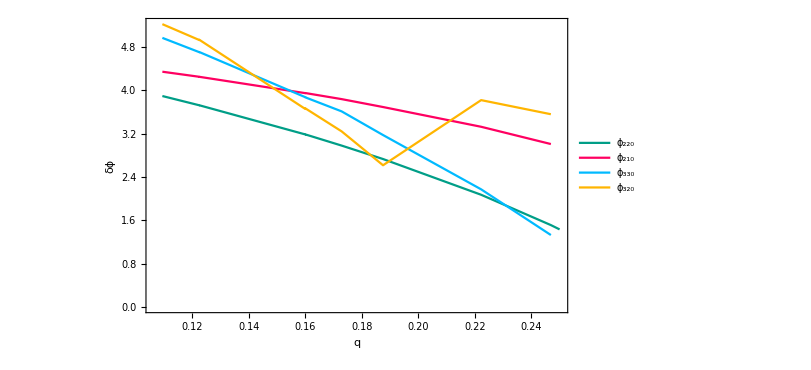

```mathematica
lp=ListLinePlot[{Transpose[{q/(q+1)^2,Mod[phse15[[All,1]],2π]}],Drop[Transpose[{q/(q+1)^2,Mod[phse15[[All,2]],2π]}],1],Drop[Transpose[{q/(q+1)^2,Mod[phse15[[All,3]],2π]}],1],
Drop[Transpose[{q/(q+1)^2,Mod[phse15[[All,4]],2π]}],1]},PlotStyle->colors,Frame->True,PlotLegends->Placed[{"ϕ_220","ϕ_210","ϕ_330","ϕ_320"},{0.85,0.8}],FrameLabel->{"q","δϕ"},ImageSize->600,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full]
```

#### n=1 (with 32)

```mathematica
(* Here start the α0,α1 contours*)
ansall=Table[
t0[index]=tmax[[index]];
mysxscase22modeRD[index]=Table[Select[sxsrhs[[index,i]],#[[1]]≥ tmax[[index]]&],{i,Length@modes}];
ans=Table[If[modes[[i,1]]==3&&modes[[i,2]]==2,mix=True,mix=False];OvertoneModel[1,{η[[index]],χ1[[index]],χ2[[index]]},"Fitα"->{},"Mode"->modes[[i]],"Mixing"->{mix,{2,2}}]/.ti->(tfit),{i,Length@modes}],{index,1,Length@tag}];
```

```mathematica
val022=Table[(Select[Arg0DStructs[mysxscase22modeRD[i][[1]]],#[[1]]≥ tmax[[i]]+tfit&,1])[[1,2]],{i,Length@tag}];
val021=Table[(Select[Arg0DStructs[mysxscase22modeRD[i][[2]]],#[[1]]≥ tmax[[i]]+tfit&,1])[[1,2]],{i,Length@tag}];
val033=Table[(Select[Arg0DStructs[mysxscase22modeRD[i][[3]]],#[[1]]≥ tmax[[i]]+tfit&,1])[[1,2]],{i,Length@tag}];
val032=Table[(Select[Arg0DStructs[mysxscase22modeRD[i][[4]]],#[[1]]≥ tmax[[i]]+tfit&,1])[[1,2]],{i,Length@tag}];
```

```mathematica
phs0={val022,val021,val033,val032}
```

{{5.21523,3.77056,4.06827,5.85542,2.04401,2.22446,4.80165,0.361813,1.54004,3.29644},{1.30762,0.444318,3.74426,1.41171,5.79803,2.73592,0.856108,1.73734,2.34928,3.22479},{3.05762,9.53213,6.81621,6.29361,6.84283,3.94551,4.66418,7.36861,2.86942,5.49252},{4.93665,3.49015,3.96705,6.39506,2.96556,3.40893,5.96559,1.92626,3.13131,4.96809}}

```mathematica
mysxscase22modeRD0sh=Table[mysxscase22modeRD[index][[j]]/.{xx_,yy_}->{xx-tmax[[index]],yy Exp[-I phs0[[j,index]]]},{index,Length@tag},{j,Length@modes}];
```

```mathematica
Chop@Mod[Table[Select[Arg0DStructs@mysxscase22modeRD0sh[[i,1]],#[[1]]≥ 10&,1][[1,2]],{i,Length@tag}],2π]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
t0ampsdataall=Table[
data=Select[mysxscase22modeRD0sh[[index,j]],#[[1]]≥i&];
ansl=ansall[[index,j]];
cfit=NonlinearModelFit[data,ansl,{x0,x1,xm0,xm1},t];
amps={x0,x1,xm0,xm1}/.cfit["BestFitParameters"];

{i,amps},{index,Length@tag},{j,Length@modes},{i,0,100}];
```

```mathematica
t0ampsdataalltest=Table[
data=Select[mysxscase22modeRD0sh[[index,j]],#[[1]]≥i&];
ansl=ansall[[index,j]];
cfit=NonlinearModelFit[data,ansl,{x0,xm0,x1,xm1},t];
cfitn=Normal@cfit;
amps={x0,x1,xm0,xm1}/.cfit["BestFitParameters"];

{i,amps},{index,Length@tag},{j,Length@modes},{i,10,10}];
```

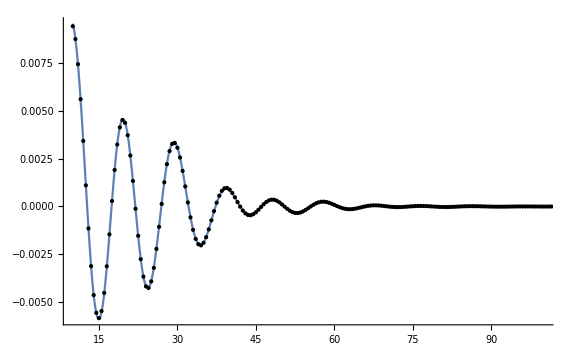

```mathematica
Plot[Re@cfitn,{t,10,100},PlotRange->All,Epilog->Point[Re@data],ImageSize->Large]
```

```mathematica
amps15=Table[Select[(Abs/@(t0ampsdataall[[i,j]])),#[[1]]≥tfit&,1][[1,2]],{i,Length@tag},{j,Length@modes}]
```

{{{0.406886,0.212648,0.,0.},{2.14976×10^-8,3.05499×10^-8,0.,0.},{2.96967×10^-8,4.75035×10^-8,0.,0.},{0.0129553,0.0131686,0.0274955,0.0208121}},{{0.416934,0.225329,0.,0.},{0.0177227,0.0119058,0.,0.},{0.0269258,0.019776,0.,0.},{0.0116759,0.0126985,0.0278052,0.0207983}},{{0.359474,0.167774,0.,0.},{0.047265,0.0297717,0.,0.},{0.066463,0.0430188,0.,0.},{0.00362583,0.00454807,0.0212718,0.0117394}},{{0.311278,0.137325,0.,0.},{0.0638624,0.0410071,0.,0.},{0.0786824,0.0464097,0.,0.},{0.00675346,0.00296998,0.0153828,0.00669854}},{{0.278873,0.114353,0.,0.},{0.0651847,0.0405206,0.,0.},{0.0845627,0.0451096,0.,0.},{0.00975833,0.00468932,0.0126063,0.00562203}},{{0.259204,0.103919,0.,0.},{0.0655693,0.0408998,0.,0.},{0.0783763,0.0441122,0.,0.},{0.0114583,0.00679521,0.0108448,0.00380878}},{{0.263329,0.108333,0.,0.},{0.0671671,0.0427672,0.,0.},{0.0795692,0.0459228,0.,0.},{0.0118087,0.00715293,0.0110765,0.00409579}},{{0.200807,0.0773494,0.,0.},{0.0637362,0.0405216,0.,0.},{0.0685959,0.0361437,0.,0.},{0.0153044,0.00975672,0.00674476,0.00367304}},{{0.199284,0.0764445,0.,0.},{0.0629463,0.0402388,0.,0.},{0.0686217,0.0371909,0.,0.},{0.0150795,0.00998066,0.00651269,0.00344969}},{{0.176297,0.0659558,0.,0.},{0.0586918,0.037217,0.,0.},{0.0627906,0.0333049,0.,0.},{0.0150914,0.0100434,0.00512764,0.00337358}}}

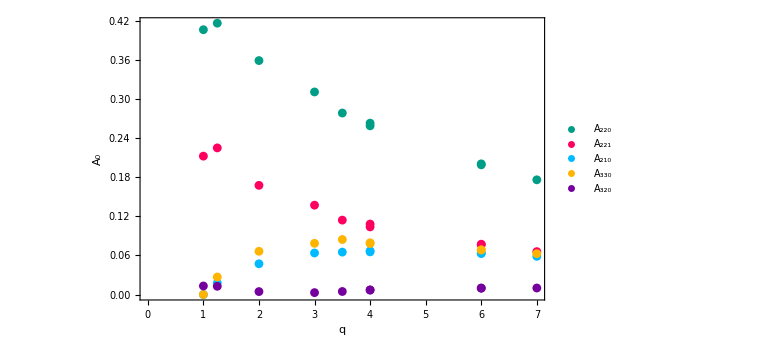

```mathematica
lp=ListPlot[{Transpose[{q,amps15[[All,1,1]]}],Transpose[{q,amps15[[All,1,2]]}],Transpose[{q,amps15[[All,2,1]]}],Transpose[{q,amps15[[All,3,1]]}],Transpose[{q,amps15[[All,4,2]]}]},PlotStyle->colors,Frame->True,PlotLegends->Placed[{"A_220","A_221","A_210","A_330","A_320"},{0.85,0.8}],FrameLabel->{"q","A_0"},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full]
```

```mathematica
mus=Table[ModeMixingFitCoeffSY[q[[i]]/(q[[i]]+1)^2,χ1[[i]],χ2[[i]],2,2,3,0],{i,Length@q}]
```

{0.097101+0.00899369 ⅈ,0.0958112+0.00895285 ⅈ,0.0721211+0.00771306 ⅈ,0.06647+0.0073044 ⅈ,0.0615404+0.00692141 ⅈ,0.0615404+0.00692141 ⅈ,0.0471044+0.00568477 ⅈ,0.0471042+0.00568475 ⅈ,0.0420416+0.00521625 ⅈ}

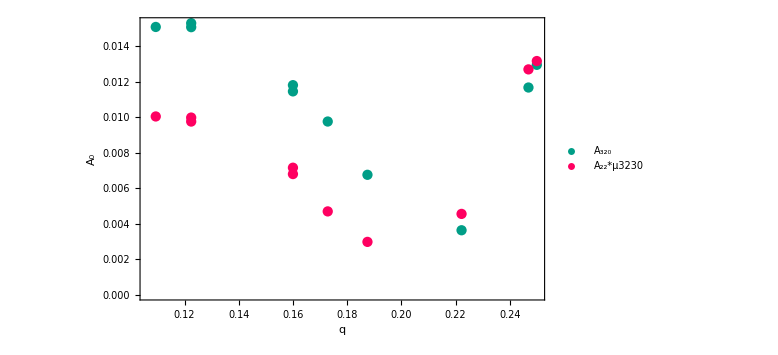
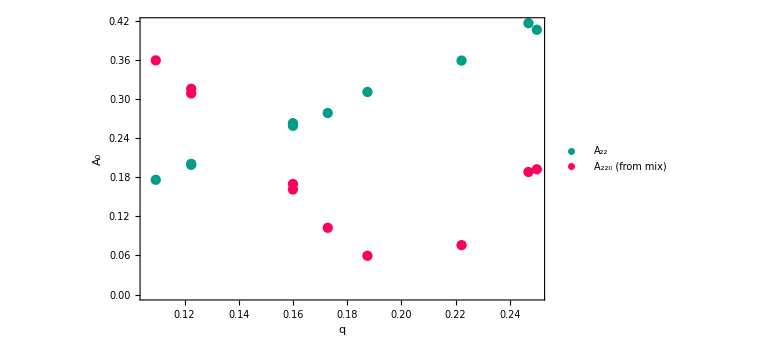

```mathematica
{ListPlot[{Transpose[{q/(q+1)^2,Abs[amps15[[All,4,1]]]}],Transpose[{q/(q+1)^2,Abs[amps15[[All,4,2]]]}]},PlotStyle->colors,Frame->True,PlotLegends->Placed[{"A_320","A_22*μ3230"},{0.15,0.8}],FrameLabel->{"q","A_0"},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full],

ListPlot[{Transpose[{q/(q+1)^2,Abs[amps15[[All,1,1]]]}],Transpose[{q/(q+1)^2,Abs[amps15[[All,4,2]]/((-1)^(-1)mus)]}]},PlotStyle->colors,Frame->True,PlotLegends->Placed[{"A_22","A_220 (from mix)"},{0.15,0.8}],FrameLabel->{"q","A_0"},ImageSize->Large,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full]}
```

```mathematica
Export["/Users/xisco/Work/INFN/Work/Rdown/plotsV2/AmpFitQ.pdf",lp]
```

/Users/xisco/Work/INFN/Work/Rdown/plotsV2/AmpFitQ.pdf

```mathematica
phse15=Table[Select[(Arg0DStructs@(Transpose[{t0ampsdataall[[i,j,All,1]],t0ampsdataall[[i,j,All,2,1]]}])),#[[1]]≥tfit&,1][[1,2]],{i,Length@tag},{j,Length@modes}]
```

{{1.43333,-3.05641,-1.32451,-2.70714},{1.51273,3.00955,1.32901,-2.72279},{2.07279,-2.95466,2.17311,-2.46239},{2.7327,-2.58999,-3.10733,2.61755},{2.98107,-2.44381,-2.67017,-3.03962},{-3.09584,-2.3316,-2.41154,-2.61448},{-3.09659,-2.3337,-2.409,-2.62651},{-2.5573,-2.03174,-1.5741,-1.34727},{-2.55771,-2.0313,-1.57675,-1.35266},{-2.38671,-1.93778,-1.31267,-1.05931}}

```mathematica
Plot[{fun220,fun221},{eta,0.,0.25},Epilog->{{Point[Transpose[{q/(q+1)^2,Mod[phse15[[All,1]],2π]}]]},{Point[Transpose[{q/(q+1)^2,Mod[phse15[[All,2]],2π]}]]}}]
```

-Graphics-

```mathematica
Drop[Transpose[{q/(q+1)^2,Mod[phse15[[All,4]],2π]}],1]
```

{{0.246914,3.5604},{0.222222,3.8208},{0.1875,2.61755},{0.17284,3.24356},{0.16,3.66871},{0.16,3.65668},{0.122449,4.93591},{0.122449,4.93052},{0.109375,5.22387}}

```mathematica
lp=ListLinePlot[{Transpose[{q/(q+1)^2,Mod[phse15[[All,1]],2π]}],Drop[Transpose[{q/(q+1)^2,Mod[phse15[[All,2]],2π]}],1],Drop[Transpose[{q/(q+1)^2,Mod[phse15[[All,3]],2π]}],1],
Drop[Transpose[{q/(q+1)^2,Mod[phse15[[All,4]],2π]}],1]},PlotStyle->colors,Frame->True,PlotLegends->Placed[{"ϕ_220","ϕ_210","ϕ_330","ϕ_320"},{0.85,0.8}],FrameLabel->{"q","δϕ"},ImageSize->600,Frame->True,FrameStyle->Directive[Black,Bold,16],LabelStyle->Directive[Black,Bold,16],GridLines->Full]
```

-Graphics-